```mathematica
Factor2=Factor[#,Modulus->2]&
```

Factor[#1,Modulus→2]&

```mathematica
Factor3=Factor[#,Modulus->3]&
```

Factor[#1,Modulus→3]&

```mathematica
ec1=y1^2+a1 x1 y1+a3 y1-x1^3-a2 x1^2-a4 x1-a6
```

-a6-a4 x1-a2 x1^2-x1^3+a3 y1+a1 x1 y1+y1^2

```mathematica
Z1^3 ec1/.{x1->X1/Z1,y1->Y1/Z1}//Expand//InputForm
```

-X1^3 - a2*X1^2*Z1 + a1*X1*Y1*Z1 + Y1^2*Z1 - a4*X1*Z1^2 + a3*Y1*Z1^2 - a6*Z1^3

```mathematica
ec2=ec1/.{x1->x2,y1->y2}
```

-a6-a4 x2-a2 x2^2-x2^3+a3 y2+a1 x2 y2+y2^2

```mathematica
Z1^3 ec1/.{X1->X1/Z1,Y1->Y1/Z1}/.{X1->X2,Y1->Y2,Z1->Z2}//Expand//InputForm
```

-(a6*Z2^3) - a4*x1*Z2^3 - a2*x1^2*Z2^3 - x1^3*Z2^3 + a3*y1*Z2^3 + a1*x1*y1*Z2^3 + y1^2*Z2^3

```mathematica
ec=Z^3ec1/.{x1->X/Z,y1->Y/Z}//Expand
```

-X^3-a2 X^2 Z+a1 X Y Z+Y^2 Z-a4 X Z^2+a3 Y Z^2-a6 Z^3

```mathematica
dec=D[ec,{{X,Y,Z}}]
```

{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}

```mathematica
ec/.{X->dec[[1]],Y->dec[[2]],Z->dec[[3]]}//Factor;
```

```mathematica
cub=X^3+Y^3+Z^3-l X Y Z
```

X^3+Y^3-l X Y Z+Z^3

```mathematica
dcub=D[cub,{{X,Y,Z}}]
```

{3 X^2-l Y Z,3 Y^2-l X Z,-l X Y+3 Z^2}

```mathematica
cub/.{X->dcub[[1]],Y->dcub[[2]],Z->dcub[[3]]}//Factor
```

27 X^6+9 l^2 X^3 Y^3-l^3 X^3 Y^3+27 Y^6-27 l X^4 Y Z-3 l^3 X^4 Y Z-27 l X Y^4 Z-3 l^3 X Y^4 Z-27 l X^2 Y^2 Z^2+27 l^2 X^2 Y^2 Z^2+l^4 X^2 Y^2 Z^2+9 l^2 X^3 Z^3-l^3 X^3 Z^3+9 l^2 Y^3 Z^3-l^3 Y^3 Z^3-27 l X Y Z^4-3 l^3 X Y Z^4+27 Z^6

```mathematica
GroebnerBasis[Join[{x,y,z}-dcub,{cub}],{X,Y,Z,x,y,z},{X,Y,Z}][[1]]
```

27 x^6-54 x^3 y^3+4 l^3 x^3 y^3+27 y^6-18 l^2 x^4 y z-18 l^2 x y^4 z+108 l x^2 y^2 z^2-l^4 x^2 y^2 z^2-54 x^3 z^3+4 l^3 x^3 z^3-54 y^3 z^3+4 l^3 y^3 z^3-18 l^2 x y z^4+27 z^6

```mathematica
ram=GroebnerBasis[Join[{x,y,z}-dcub,{cub}],{X,Y,Z,x,y,z},{X,Y,Z}][[1]]
```

27 x^6-54 x^3 y^3+4 l^3 x^3 y^3+27 y^6-18 l^2 x^4 y z-18 l^2 x y^4 z+108 l x^2 y^2 z^2-l^4 x^2 y^2 z^2-54 x^3 z^3+4 l^3 x^3 z^3-54 y^3 z^3+4 l^3 y^3 z^3-18 l^2 x y z^4+27 z^6

```mathematica
X3c=w^2-ram/27;
```

```mathematica
X33c=w^2-ram;
```

```mathematica
X3c/.{l->1}//Expand
```

w^2-x^6+(50 x^3 y^3)/27-y^6+2/3 x^4 y z+2/3 x y^4 z-107/27 x^2 y^2 z^2+(50 x^3 z^3)/27+(50 y^3 z^3)/27+2/3 x y z^4-z^6

```mathematica
X33c/.{l->1}//Factor3
```

w^2+2 x^3 y^3+x^2 y^2 z^2+2 x^3 z^3+2 y^3 z^3

```mathematica
ddcub=D[cub,{{X,Y,Z},2}]//Det
```

-6 l^2 X^3-6 l^2 Y^3+216 X Y Z-2 l^3 X Y Z-6 l^2 Z^3

```mathematica
ddcub//Factor[#,Modulus->3]&
```

l^3 X Y Z

```mathematica
infpts=Solve[#==0&/@Join[{cub},{ddcub}],{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{X→0,Z→-Y},{X→0,Z→(-1)^(1/3) Y},{X→0,Z→-(-1)^(2/3) Y},{Y→0,Z→-X},{Y→0,Z→(-1)^(1/3) X},{Y→0,Z→-(-1)^(2/3) X},{Y→-X,Z→0},{Y→(-1)^(1/3) X,Z→0},{Y→-(-1)^(2/3) X,Z→0}}

```mathematica
dcub/Y^2/.{X->0,Z->-Y}
```

{l,3,3}

```mathematica
dX3c=D[X3c,{{x,y,z,w}}]//Factor
```

{-2/27 (81 x^5-81 x^2 y^3+6 l^3 x^2 y^3-36 l^2 x^3 y z-9 l^2 y^4 z+108 l x y^2 z^2-l^4 x y^2 z^2-81 x^2 z^3+6 l^3 x^2 z^3-9 l^2 y z^4),2/27 (81 x^3 y^2-6 l^3 x^3 y^2-81 y^5+9 l^2 x^4 z+36 l^2 x y^3 z-108 l x^2 y z^2+l^4 x^2 y z^2+81 y^2 z^3-6 l^3 y^2 z^3+9 l^2 x z^4),2/27 (9 l^2 x^4 y+9 l^2 x y^4-108 l x^2 y^2 z+l^4 x^2 y^2 z+81 x^3 z^2-6 l^3 x^3 z^2+81 y^3 z^2-6 l^3 y^3 z^2+36 l^2 x y z^3-81 z^5),2 w}

```mathematica
Solve[#==0&/@Join[dX3c,{X3c}],{x,y,z,w}]//Factor//DeleteDuplicates
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→(l y)/3,z→y,w→0},{x→1/3 (-1)^(2/3) l y,z→-(-1)^(1/3) y,w→0},{x→-1/3 (-1)^(1/3) l y,z→(-1)^(2/3) y,w→0},{x→(3 y)/l,z→(3 y)/l,w→0},{x→y,z→(l y)/3,w→0},{x→(6 y)/((-1-ⅈ √3) l),z→-(3 ⅈ (-ⅈ+√3) y)/(2 l),w→0},{x→(6 y)/((-1+ⅈ √3) l),z→(3 ⅈ (ⅈ+√3) y)/(2 l),w→0},{x→(2 y)/(-1-ⅈ √3),z→-1/6 ⅈ (-ⅈ+√3) l y,w→0},{x→(2 y)/(-1+ⅈ √3),z→1/6 ⅈ (ⅈ+√3) l y,w→0},{x→0,y→0,z→0,w→0}}

```mathematica
daltcub={dcub[[3]],dcub[[1]]+dcub[[2]],(dcub[[1]]dcub[[2]])}//Factor
```

{-l X Y+3 Z^2,3 X^2+3 Y^2-l X Z-l Y Z,-((3 Y^2-l X Z) (-3 X^2+l Y Z))}

```mathematica
dcub
```

{3 X^2-l Y Z,3 Y^2-l X Z,-l X Y+3 Z^2}

```mathematica
X6c=d^2-(b^2-4c)GroebnerBasis[Join[{a,b,c}-daltcub,{cub}],{X,Y,Z,a,b,c},{X,Y,Z}][[1]]/27//Expand
```

-a^6 b^2+2 a^3 b^5-b^8+4 a^6 c-14 a^3 b^3 c+10 b^6 c+24 a^3 b c^2-33 b^4 c^2+40 b^2 c^3-16 c^4+d^2-4 a^2 b^2 c^2 l+16 a^2 c^3 l+2/3 a^4 b^2 c l^2+2/3 a b^5 c l^2-8/3 a^4 c^2 l^2-14/3 a b^3 c^2 l^2+8 a b c^3 l^2-4/27 a^3 b^5 l^3+28/27 a^3 b^3 c l^3-16/9 a^3 b c^2 l^3-4/27 b^2 c^3 l^3+(16 c^4 l^3)/27+1/27 a^2 b^2 c^2 l^4-4/27 a^2 c^3 l^4

```mathematica
X6c/.{l->1}//Expand
```

-a^6 b^2+(50 a^3 b^5)/27-b^8+4 a^6 c+2/3 a^4 b^2 c-350/27 a^3 b^3 c+2/3 a b^5 c+10 b^6 c-(8 a^4 c^2)/3+200/9 a^3 b c^2-107/27 a^2 b^2 c^2-14/3 a b^3 c^2-33 b^4 c^2+(428 a^2 c^3)/27+8 a b c^3+(1076 b^2 c^3)/27-(416 c^4)/27+d^2

```mathematica
dX6c=D[X6c,{{a,b,c,d}}]//Factor
```

{-2/27 (b^2-4 c) (81 a^5-81 a^2 b^3+243 a^2 b c+108 a c^2 l-36 a^3 c l^2-9 b^3 c l^2+27 b c^2 l^2+6 a^2 b^3 l^3-18 a^2 b c l^3-a c^2 l^4),-2/27 (27 a^6 b-135 a^3 b^4+108 b^7+567 a^3 b^2 c-810 b^5 c-324 a^3 c^2+1782 b^3 c^2-1080 b c^3+108 a^2 b c^2 l-18 a^4 b c l^2-45 a b^4 c l^2+189 a b^2 c^2 l^2-108 a c^3 l^2+10 a^3 b^4 l^3-42 a^3 b^2 c l^3+24 a^3 c^2 l^3+4 b c^3 l^3-a^2 b c^2 l^4),2/27 (54 a^6-189 a^3 b^3+135 b^6+648 a^3 b c-891 b^4 c+1620 b^2 c^2-864 c^3-108 a^2 b^2 c l+648 a^2 c^2 l+9 a^4 b^2 l^2+9 a b^5 l^2-72 a^4 c l^2-126 a b^3 c l^2+324 a b c^2 l^2+14 a^3 b^3 l^3-48 a^3 b c l^3-6 b^2 c^2 l^3+32 c^3 l^3+a^2 b^2 c l^4-6 a^2 c^2 l^4),2 d}

```mathematica
Solve[#==0&/@Join[dX6c,{X6c}],{a,b,c,d}]//Factor//PowerExpand//DeleteDuplicates
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→-(b l)/3,c→b^2,d→0},{a→(b l)/6,c→b^2/4,d→0},{a→(3 b)/(3+l),c→(3 b^2 l)/(3+l)^2,d→0},{a→-(3 (3 b+ⅈ √3 b (-3+l)+b l))/(2 (9-3 l+l^2)),c→(3 (-6887475360 ⅈ √3 b^5 (-3+l)+2142770112 ⅈ √3 b^5 (-3+l)^3-153055008 ⅈ √3 b^5 (-3+l)^5-22039921152 b^5 l+6772684104 ⅈ √3 b^5 (-3+l) l-229582512 ⅈ √3 b^5 (-3+l)^3 l-12754584 ⅈ √3 b^5 (-3+l)^5 l+64283103360 b^5 l^2-5165606520 ⅈ √3 b^5 (-3+l) l^2+297606960 ⅈ √3 b^5 (-3+l)^3 l^2+4251528 ⅈ √3 b^5 (-3+l)^5 l^2-55099802880 b^5 l^3+1715491548 ⅈ √3 b^5 (-3+l) l^3+127545840 ⅈ √3 b^5 (-3+l)^3 l^3-6377292 ⅈ √3 b^5 (-3+l)^5 l^3+24233709600 b^5 l^4-367757172 ⅈ √3 b^5 (-3+l) l^4-76527504 ⅈ √3 b^5 (-3+l)^3 l^4-708588 ⅈ √3 b^5 (-3+l)^5 l^4-6870469248 b^5 l^5+19131876 ⅈ √3 b^5 (-3+l) l^5+33539832 ⅈ √3 b^5 (-3+l)^3 l^5+236196 ⅈ √3 b^5 (-3+l)^5 l^5+1258452288 b^5 l^6-20076660 ⅈ √3 b^5 (-3+l) l^6-4461480 ⅈ √3 b^5 (-3+l)^3 l^6-26244 ⅈ √3 b^5 (-3+l)^5 l^6-69914016 b^5 l^7+27064125 ⅈ √3 b^5 (-3+l) l^7-1718982 ⅈ √3 b^5 (-3+l)^3 l^7-2187 ⅈ √3 b^5 (-3+l)^5 l^7-101721744 b^5 l^8-11986947 ⅈ √3 b^5 (-3+l) l^8+325134 ⅈ √3 b^5 (-3+l)^3 l^8+729 ⅈ √3 b^5 (-3+l)^5 l^8+64875168 b^5 l^9+3153654 ⅈ √3 b^5 (-3+l) l^9-48114 ⅈ √3 b^5 (-3+l)^3 l^9-13471920 b^5 l^10+190998 ⅈ √3 b^5 (-3+l) l^10-16038 ⅈ √3 b^5 (-3+l)^3 l^10-1866240 b^5 l^11-404595 ⅈ √3 b^5 (-3+l) l^11+4536 ⅈ √3 b^5 (-3+l)^3 l^11+1947888 b^5 l^12+157869 ⅈ √3 b^5 (-3+l) l^12-1152 ⅈ √3 b^5 (-3+l)^3 l^12-632448 b^5 l^13-36504 ⅈ √3 b^5 (-3+l) l^13+144 ⅈ √3 b^5 (-3+l)^3 l^13+123552 b^5 l^14+5184 ⅈ √3 b^5 (-3+l) l^14-16 ⅈ √3 b^5 (-3+l)^3 l^14-16416 b^5 l^15-480 ⅈ √3 b^5 (-3+l) l^15+1392 b^5 l^16+16 ⅈ √3 b^5 (-3+l) l^16-64 b^5 l^17))/(4 (-3+l) (9-3 l+l^2)^2 (-408146688 b^3+51018336 ⅈ √3 b^3 (-3+l)-5668704 ⅈ √3 b^3 (-3+l)^3+357128352 b^3 l-17006112 ⅈ √3 b^3 (-3+l) l-164392416 b^3 l^2+13226976 ⅈ √3 b^3 (-3+l) l^2+51963120 b^3 l^3-2204496 ⅈ √3 b^3 (-3+l) l^3-314928 ⅈ √3 b^3 (-3+l)^3 l^3-5983632 b^3 l^4+1259712 ⅈ √3 b^3 (-3+l) l^4-2414448 b^3 l^5-69984 ⅈ √3 b^3 (-3+l) l^5+2029536 b^3 l^6+11664 ⅈ √3 b^3 (-3+l) l^6-3888 ⅈ √3 b^3 (-3+l)^3 l^6-574452 b^3 l^7+20412 ⅈ √3 b^3 (-3+l) l^7+6804 b^3 l^8-8424 ⅈ √3 b^3 (-3+l) l^8+39528 b^3 l^9+1971 ⅈ √3 b^3 (-3+l) l^9-27 ⅈ √3 b^3 (-3+l)^3 l^9-15120 b^3 l^10-162 ⅈ √3 b^3 (-3+l) l^10+2664 b^3 l^11-21 ⅈ √3 b^3 (-3+l) l^11-288 b^3 l^12+8 ⅈ √3 b^3 (-3+l) l^12+8 b^3 l^13)),d→0},{a→-(3 (3 b-ⅈ √3 b (-3+l)+b l))/(2 (9-3 l+l^2)),c→(3 (-6887475360 ⅈ √3 b^5 (-3+l)+2142770112 ⅈ √3 b^5 (-3+l)^3-153055008 ⅈ √3 b^5 (-3+l)^5+22039921152 b^5 l+6772684104 ⅈ √3 b^5 (-3+l) l-229582512 ⅈ √3 b^5 (-3+l)^3 l-12754584 ⅈ √3 b^5 (-3+l)^5 l-64283103360 b^5 l^2-5165606520 ⅈ √3 b^5 (-3+l) l^2+297606960 ⅈ √3 b^5 (-3+l)^3 l^2+4251528 ⅈ √3 b^5 (-3+l)^5 l^2+55099802880 b^5 l^3+1715491548 ⅈ √3 b^5 (-3+l) l^3+127545840 ⅈ √3 b^5 (-3+l)^3 l^3-6377292 ⅈ √3 b^5 (-3+l)^5 l^3-24233709600 b^5 l^4-367757172 ⅈ √3 b^5 (-3+l) l^4-76527504 ⅈ √3 b^5 (-3+l)^3 l^4-708588 ⅈ √3 b^5 (-3+l)^5 l^4+6870469248 b^5 l^5+19131876 ⅈ √3 b^5 (-3+l) l^5+33539832 ⅈ √3 b^5 (-3+l)^3 l^5+236196 ⅈ √3 b^5 (-3+l)^5 l^5-1258452288 b^5 l^6-20076660 ⅈ √3 b^5 (-3+l) l^6-4461480 ⅈ √3 b^5 (-3+l)^3 l^6-26244 ⅈ √3 b^5 (-3+l)^5 l^6+69914016 b^5 l^7+27064125 ⅈ √3 b^5 (-3+l) l^7-1718982 ⅈ √3 b^5 (-3+l)^3 l^7-2187 ⅈ √3 b^5 (-3+l)^5 l^7+101721744 b^5 l^8-11986947 ⅈ √3 b^5 (-3+l) l^8+325134 ⅈ √3 b^5 (-3+l)^3 l^8+729 ⅈ √3 b^5 (-3+l)^5 l^8-64875168 b^5 l^9+3153654 ⅈ √3 b^5 (-3+l) l^9-48114 ⅈ √3 b^5 (-3+l)^3 l^9+13471920 b^5 l^10+190998 ⅈ √3 b^5 (-3+l) l^10-16038 ⅈ √3 b^5 (-3+l)^3 l^10+1866240 b^5 l^11-404595 ⅈ √3 b^5 (-3+l) l^11+4536 ⅈ √3 b^5 (-3+l)^3 l^11-1947888 b^5 l^12+157869 ⅈ √3 b^5 (-3+l) l^12-1152 ⅈ √3 b^5 (-3+l)^3 l^12+632448 b^5 l^13-36504 ⅈ √3 b^5 (-3+l) l^13+144 ⅈ √3 b^5 (-3+l)^3 l^13-123552 b^5 l^14+5184 ⅈ √3 b^5 (-3+l) l^14-16 ⅈ √3 b^5 (-3+l)^3 l^14+16416 b^5 l^15-480 ⅈ √3 b^5 (-3+l) l^15-1392 b^5 l^16+16 ⅈ √3 b^5 (-3+l) l^16+64 b^5 l^17))/(4 (-3+l) (9-3 l+l^2)^2 (408146688 b^3+51018336 ⅈ √3 b^3 (-3+l)-5668704 ⅈ √3 b^3 (-3+l)^3-357128352 b^3 l-17006112 ⅈ √3 b^3 (-3+l) l+164392416 b^3 l^2+13226976 ⅈ √3 b^3 (-3+l) l^2-51963120 b^3 l^3-2204496 ⅈ √3 b^3 (-3+l) l^3-314928 ⅈ √3 b^3 (-3+l)^3 l^3+5983632 b^3 l^4+1259712 ⅈ √3 b^3 (-3+l) l^4+2414448 b^3 l^5-69984 ⅈ √3 b^3 (-3+l) l^5-2029536 b^3 l^6+11664 ⅈ √3 b^3 (-3+l) l^6-3888 ⅈ √3 b^3 (-3+l)^3 l^6+574452 b^3 l^7+20412 ⅈ √3 b^3 (-3+l) l^7-6804 b^3 l^8-8424 ⅈ √3 b^3 (-3+l) l^8-39528 b^3 l^9+1971 ⅈ √3 b^3 (-3+l) l^9-27 ⅈ √3 b^3 (-3+l)^3 l^9+15120 b^3 l^10-162 ⅈ √3 b^3 (-3+l) l^10-2664 b^3 l^11-21 ⅈ √3 b^3 (-3+l) l^11+288 b^3 l^12+8 ⅈ √3 b^3 (-3+l) l^12-8 b^3 l^13)),d→0},{a→(b^2 l^2-b l (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)+(54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(2/3))/(6 (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)),c→b^2/4,d→0},{a→(ⅈ (b l+(54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)) (ⅈ b l-√3 b l+ⅈ (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)+√3 (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)))/(12 (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)),c→b^2/4,d→0},{a→-(ⅈ (b l+(54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)) (-ⅈ b l-√3 b l-ⅈ (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)+√3 (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)))/(12 (54 b^3-b^3 l^3+6 ⅈ √3 b^3 √(-27+l^3))^(1/3)),c→b^2/4,d→0},{a→0,b→0,c→0,d→0}}

```mathematica
TakePairs[list_]:=Table[list[[i]]list[[j]],{i,1,Length[list]},{j,1,i}]//Flatten
TakeTriples[list_]:=Table[list[[i]]list[[j]] list[[k]],{i,1,Length[list]},{j,1,i},{k,1,j}]//Flatten
TakeQuads[list_]:=Table[list[[i]]list[[j]] list[[k]] list[[l]],{i,1,Length[list]},{j,1,i},{k,1,j},{l,1,k}]//Flatten
```

```mathematica
Join[TakeTriples[{x,y,z}],{w}]//InputForm
```

{x^3, x^2*y, x*y^2, y^3, x^2*z, x*y*z, y^2*z, x*z^2, y*z^2, z^3, w}

```mathematica
%//Length
```

11

```mathematica
Join[{x,y,z}-dec,{ec}]
```

{x+3 X^2+2 a2 X Z-a1 Y Z+a4 Z^2,y-a1 X Z-2 Y Z-a3 Z^2,a2 X^2-a1 X Y-Y^2+z+2 a4 X Z-2 a3 Y Z+3 a6 Z^2,-X^3-a2 X^2 Z+a1 X Y Z+Y^2 Z-a4 X Z^2+a3 Y Z^2-a6 Z^3}

```mathematica
(*ram=GroebnerBasis[Join[{x,y,z}-dec,{ec}],{X,Y,Z,x,y,z},{X,Y,Z}][[1]]
```

```mathematica
X3c=w^2-ram/27;
```

```mathematica
ec//InputForm
```

-X^3 - a2*X^2*Z + a1*X*Y*Z + Y^2*Z - a4*X*Z^2 + a3*Y*Z^2 - a6*Z^3

```mathematica
CoefficientArrays[{{x,y,z},{X1,Y1,Z1},{X2,Y2,Z2}}//Det,{x,y,z}][[2]]//Normal//InputForm
```

{-(Y2*Z1) + Y1*Z2, X2*Z1 - X1*Z2, -(X2*Y1) + X1*Y2}

```mathematica
x^6+2*x^5*y-x^4*y^2-8*x^3*y^3-13*x^2*y^4-10*x*y^5-3*y^6-4*x^5*z-4*x^4*y*z+14*x^3*y^2*z+38*x^2*y^3*z+38*x*y^4*z+14*y^5*z+4*x^4*z^2+6*x^3*y*z^2-38*x^2*y^2*z^2-54*x*y^3*z^2-41*y^4*z^2-4*x^3*z^3+36*x*y^2*z^3+54*y^3*z^3-27*y^2*z^4//Factor2
```

(x^3+x^2 y+x y^2+y^3+y^2 z+y z^2)^2

```mathematica
((x^6+2*x^5*y-x^4*y^2-8*x^3*y^3-13*x^2*y^4-10*x*y^5-3*y^6-4*x^5*z-4*x^4*y*z+14*x^3*y^2*z+38*x^2*y^3*z+38*x*y^4*z+14*y^5*z+4*x^4*z^2+6*x^3*y*z^2-38*x^2*y^2*z^2-54*x*y^3*z^2-41*y^4*z^2-4*x^3*z^3+36*x*y^2*z^3+54*y^3*z^3-27*y^2*z^4)-(x^3+x^2 y+x y^2+y^3+y^2 z+y z^2)^2)/4//Factor//Factor2
```

x^4 y^2+x^3 y^3+x y^5+y^6+x^5 z+x^4 y z+x^3 y^2 z+x^2 y^3 z+x y^4 z+y^5 z+x^4 z^2+x^3 y z^2+y^4 z^2+x^3 z^3+x y^2 z^3+y^3 z^3+y^2 z^4

```mathematica
PolynomialReduce[x^4 y^2+x^3 y^3+x y^5+y^6+x^5 z+x^4 y z+x^3 y^2 z+x^2 y^3 z+x y^4 z+y^5 z+x^4 z^2+x^3 y z^2+y^4 z^2+x^3 z^3+x y^2 z^3+y^3 z^3+y^2 z^4,(x^3+x^2 y+x y^2+y^3+y^2 z+y z^2),{x,y,z},Modulus->2]
```

{{x y^2+x^2 z+x z^2+z^3},x^2 y^4+y^6+y^5 z+y^4 z^2+x y^2 z^3+x y z^4+y z^5}

```mathematica
ec
```

-X^3-a2 X^2 Z+a1 X Y Z+Y^2 Z-a4 X Z^2+a3 Y Z^2-a6 Z^3

```mathematica
ec1
```

-a6-a4 x1-a2 x1^2-x1^3+a3 y1+a1 x1 y1+y1^2

```mathematica
linex=InterpolatingPolynomial[{{x1,y1},{x2,y2}},x]
```

y1+((x-x1) (-y1+y2))/(-x1+x2)

```mathematica
ec1
```

-a6-a4 x1-a2 x1^2-x1^3+a3 y1+a1 x1 y1+y1^2

```mathematica
ec/.{Z->1,X->x,Y->linex}//Factor
```

-1/(x1-x2)^2(a6 x1^2+a4 x x1^2+a2 x^2 x1^2+x^3 x1^2-2 a6 x1 x2-2 a4 x x1 x2-2 a2 x^2 x1 x2-2 x^3 x1 x2+a6 x2^2+a4 x x2^2+a2 x^2 x2^2+x^3 x2^2-a3 x x1 y1-a1 x^2 x1 y1+a3 x x2 y1+a1 x^2 x2 y1+a3 x1 x2 y1+a1 x x1 x2 y1-a3 x2^2 y1-a1 x x2^2 y1-x^2 y1^2+2 x x2 y1^2-x2^2 y1^2+a3 x x1 y2+a1 x^2 x1 y2-a3 x1^2 y2-a1 x x1^2 y2-a3 x x2 y2-a1 x^2 x2 y2+a3 x1 x2 y2+a1 x x1 x2 y2+2 x^2 y1 y2-2 x x1 y1 y2-2 x x2 y1 y2+2 x1 x2 y1 y2-x^2 y2^2+2 x x1 y2^2-x1^2 y2^2)

```mathematica
%82/.{x->x1}//Factor
```

{{{{0,0},{x1,y}},{{0,1},{x1+y,-x1}},{{0,2},{y,-x1-y}},{{0,3},{-x1,-y}},{{0,4},{-x1-y,x1}},{{0,5},{-y,x1+y}}},{{{1,0},{-x1,y}},{{1,1},{-x1-y,-x1}},{{1,2},{-y,-x1-y}},{{1,3},{x1,-y}},{{1,4},{x1+y,x1}},{{1,5},{y,x1+y}}}}

```mathematica
ec1
```

-a6-a4 x1-a2 x1^2-x1^3+a3 y1+a1 x1 y1+y1^2

```mathematica
a3 y1+a1 x1 y1+y1^2//Factor
```

y1 (a3+a1 x1+y1)

```mathematica
sumpt=Solve[(PolynomialReduce[(x1-x2)^2 ec/.{Z->1,X->x,Y->linex}//Factor,{(x-x1)(x-x2),ec1,ec2},{X,y1,y2,x2,x1}][[1,1]]//Factor)==0,x
][[1]]
```

{x→(2 a6+a4 x1+a4 x2+2 a2 x1 x2+x1^2 x2+x1 x2^2-a3 y1-a1 x2 y1-a3 y2-a1 x1 y2-2 y1 y2)/(x1-x2)^2}

```mathematica
rulesx3=Join[sumpt/.{x->x3},{y3->linex/.sumpt}//Factor]
```

{x3→(2 a6+a4 x1+a4 x2+2 a2 x1 x2+x1^2 x2+x1 x2^2-a3 y1-a1 x2 y1-a3 y2-a1 x1 y2-2 y1 y2)/(x1-x2)^2,y3→-1/(x1-x2)^3(-2 a6 y1-a4 x1 y1-a4 x2 y1-2 a2 x1 x2 y1-3 x1 x2^2 y1+x2^3 y1+a3 y1^2+a1 x2 y1^2+2 a6 y2+a4 x1 y2-x1^3 y2+a4 x2 y2+2 a2 x1 x2 y2+3 x1^2 x2 y2+a1 x1 y1 y2-a1 x2 y1 y2+2 y1^2 y2-a3 y2^2-a1 x1 y2^2-2 y1 y2^2)}

```mathematica
(ec1/.{a1->0,a2->1,a3->1,a4->1,a6->0})
```

-x1-x1^2-x1^3+y1+y1^2

```mathematica
coef={a1->0,a2->-2.4,a3->1,a4->1,a6->0}
```

{a1→0,a2→-2.4,a3→1,a4→1,a6→0}

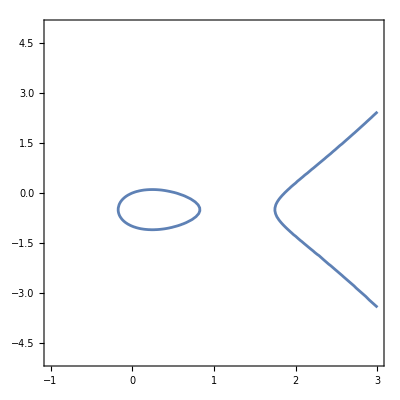

```mathematica
plote=ContourPlot[(ec1/.coef)==0,{x1,-1,3},{y1,-5,5}]
```

```mathematica
{x1,y1}/.Solve[{(ec1/.coef)==0,x1==1/2},{y1,x1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.5,-1.0244},{0.5,0.0244044}}

```mathematica
pts1=ListPlot[{x1,y1}/.Solve[{(ec1/.coef)==0,x1==1/2},{y1,x1}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
pts2=ListPlot[{x1,y1}/.Solve[{(ec1/.coef)==0,x1==0},{y1,x1}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
{{x3,y3}}/.rulesx3/.coef
```

{{(x1+x2-4.8 x1 x2+x1^2 x2+x1 x2^2-y1-y2-2 y1 y2)/(x1-x2)^2,-(-x1 y1-x2 y1+4.8 x1 x2 y1-3 x1 x2^2 y1+x2^3 y1+y1^2+x1 y2-x1^3 y2+x2 y2-4.8 x1 x2 y2+3 x1^2 x2 y2+2 y1^2 y2-y2^2-2 y1 y2^2)/(x1-x2)^3}}

```mathematica
{x1->pts1[[1,1]],y1->pts1[[1,2]],x2->pts2[[2,1]],y2->pts2[[2,2]]}
```

{x1→{},y1→{{{Directive[PointSize[0.0128333],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[2]],Point[{{0.5,-1.0244},{0.5,0.0244044}}]}}},x2→DisplayFunction→Identity,y2→DisplayFunction→Identity}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

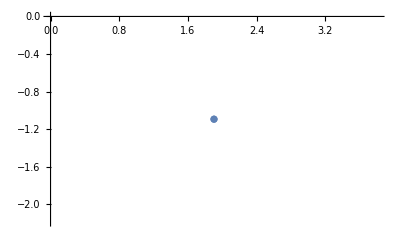

```mathematica
pts3=ListPlot[{{x3,y3}}/.rulesx3/.coef/.Solve[{(ec1/.coef)==0,x1==1/2},{y1,x1}][[1]]/.Solve[{(ec2/.coef)==0,x2==0},{y2,x2}][[1]]]
```

```mathematica
(y-linex/.Solve[{(ec1/.coef)==0,x1==1/2},{y1,x1}][[1]]/.Solve[{(ec2/.coef)==0,x2==0},{y2,x2}][[1]])
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.0244+0.0488088 (-0.5+x)+y

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

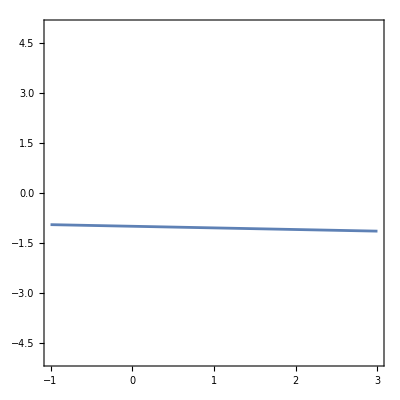

```mathematica
lineplot=ContourPlot[(y-linex/.Solve[{(ec1/.coef)==0,x1==1/2},{y1,x1}][[1]]/.Solve[{(ec2/.coef)==0,x2==0},{y2,x2}][[1]])==0,{x,-1,3},{y,-5,5}]
```

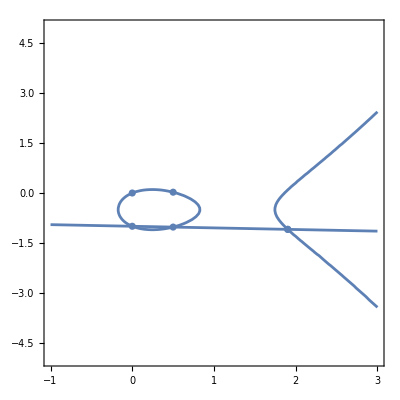

```mathematica
Show[plote, pts1,pts2,pts3,lineplot]
```

```mathematica
{x3,y3}/.rulesx3/.{x1->X1/Z1,x2->X2/Z2,y1->Y1/Z1,y2->Y2/Z2}//Factor
```

{(X1 X2^2 Z1+X1^2 X2 Z2+2 a2 X1 X2 Z1 Z2-a1 X2 Y1 Z1 Z2-a1 X1 Y2 Z1 Z2-2 Y1 Y2 Z1 Z2+a4 X2 Z1^2 Z2-a3 Y2 Z1^2 Z2+a4 X1 Z1 Z2^2-a3 Y1 Z1 Z2^2+2 a6 Z1^2 Z2^2)/(-X2 Z1+X1 Z2)^2,1/(-X2 Z1+X1 Z2)^3(-X2^3 Y1 Z1^2+3 X1 X2^2 Y1 Z1 Z2-3 X1^2 X2 Y2 Z1 Z2-2 a2 X1 X2 Y2 Z1^2 Z2+a1 X2 Y1 Y2 Z1^2 Z2+a1 X1 Y2^2 Z1^2 Z2+2 Y1 Y2^2 Z1^2 Z2-a4 X2 Y2 Z1^3 Z2+a3 Y2^2 Z1^3 Z2+X1^3 Y2 Z2^2+2 a2 X1 X2 Y1 Z1 Z2^2-a1 X2 Y1^2 Z1 Z2^2-a1 X1 Y1 Y2 Z1 Z2^2-2 Y1^2 Y2 Z1 Z2^2+a4 X2 Y1 Z1^2 Z2^2-a4 X1 Y2 Z1^2 Z2^2-2 a6 Y2 Z1^3 Z2^2+a4 X1 Y1 Z1 Z2^3-a3 Y1^2 Z1 Z2^3+2 a6 Y1 Z1^2 Z2^3)}

```mathematica
-x^6-2*x^5*y+x^4*y^2+8*x^3*y^3+13*x^2*y^4+10*x*y^5+3*y^6+4*x^5*z+4*x^4*y*z-14*x^3*y^2*z-38*x^2*y^3*z-38*x*y^4*z-14*y^5*z-4*x^4*z^2-6*x^3*y*z^2+38*x^2*y^2*z^2+54*x*y^3*z^2+41*y^4*z^2+4*x^3*z^3-36*x*y^2*z^3-54*y^3*z^3+27*y^2*z^4+w^2/.{x->-(Y2*Z1)+Y1*Z2,y->X2*Z1-X1*Z2,z->-(X2*Y1)+X1*Y2,w->0}//Factor2
```

(X2^3 Y1^2 Z1+X1^2 X2 Y2^2 Z1+X2^3 Y1 Z1^2+X1 X2^2 Y2 Z1^2+X2^3 Z1^3+X2^2 Y2 Z1^3+X2 Y2^2 Z1^3+Y2^3 Z1^3+X1 X2^2 Y1^2 Z2+X1^3 Y2^2 Z2+X1 X2^2 Z1^2 Z2+X2^2 Y1 Z1^2 Z2+X1 Y2^2 Z1^2 Z2+Y1 Y2^2 Z1^2 Z2+X1^2 X2 Y1 Z2^2+X1^3 Y2 Z2^2+X1^2 X2 Z1 Z2^2+X2 Y1^2 Z1 Z2^2+X1^2 Y2 Z1 Z2^2+Y1^2 Y2 Z1 Z2^2+X1^3 Z2^3+X1^2 Y1 Z2^3+X1 Y1^2 Z2^3+Y1^3 Z2^3)^2

```mathematica
dec
```

{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}

```mathematica
ec
```

-X^3-a2 X^2 Z+a1 X Y Z+Y^2 Z-a4 X Z^2+a3 Y Z^2-a6 Z^3

```mathematica
system=CoefficientList[PolynomialReduce[Plus@@(Table[a[i,j,6-i-j]x^i y^j z^(6-i-j),{i,0,6},{j,0,6-i}]//Flatten)/.{x->dec[[1]],y->dec[[2]],z->dec[[3]]},ec,{Y,X,Z}][[2]],{X,Y,Z}]//Flatten;
```

```mathematica
PolynomialReduce[Plus@@(Table[a[i,j,6-i-j]x^i y^j z^(6-i-j),{i,0,6},{j,0,6-i}]//Flatten)/.{x->dec[[1]],y->dec[[2]],z->dec[[3]]},ec,{Y,X,Z}][[2]]
```

```mathematica
system//Remove0//Dimensions
```

{1}

```mathematica
system
```

```mathematica
as=Table[a[i,j,6-i-j],{i,0,6},{j,0,6-i}]//Flatten
```

{a[0,0,6],a[0,1,5],a[0,2,4],a[0,3,3],a[0,4,2],a[0,5,1],a[0,6,0],a[1,0,5],a[1,1,4],a[1,2,3],a[1,3,2],a[1,4,1],a[1,5,0],a[2,0,4],a[2,1,3],a[2,2,2],a[2,3,1],a[2,4,0],a[3,0,3],a[3,1,2],a[3,2,1],a[3,3,0],a[4,0,2],a[4,1,1],a[4,2,0],a[5,0,1],a[5,1,0],a[6,0,0]}

```mathematica
ram=(a3^2+4 a6)(x^6+(-2*a1*a3^2-12*a1*a6+2*a3*a4)/(a3^2+4*a6)*x^5*y+(a1^2*a3^2+12*a1^2*a6-4*a1*a3*a4-2*a2*a3^2-12*a2*a6+a4^2)/(a3^2+4*a6)*x^4*y^2+(-4*a1^3*a6+2*a1^2*a3*a4+2*a1*a2*a3^2+24*a1*a2*a6-2*a1*a4^2-4*a2*a3*a4-4*a3^3-18*a3*a6)/(a3^2+4*a6)*x^3*y^3+(-12*a1^2*a2*a6+a1^2*a4^2+4*a1*a2*a3*a4+18*a1*a3*a6+a2^2*a3^2+12*a2^2*a6-2*a2*a4^2-12*a3^2*a4-18*a4*a6)/(a3^2+4*a6)*x^2*y^4+(-12*a1*a2^2*a6+2*a1*a2*a4^2+18*a1*a4*a6+2*a2^2*a3*a4+18*a2*a3*a6-12*a3*a4^2)/(a3^2+4*a6)*x*y^5+(-4*a2^3*a6+a2^2*a4^2+18*a2*a4*a6-4*a4^3-27*a6^2)/(a3^2+4*a6)*y^6+(-2*a1*a3-4*a4)/(a3^2+4*a6)*x^5*z+(4*a1^2*a3+10*a1*a4-4*a2*a3)/(a3^2+4*a6)*x^4*y*z+(-2*a1^3*a3-8*a1^2*a4+12*a1*a2*a3+8*a2*a4+6*a3^2+36*a6)/(a3^2+4*a6)*x^3*y^2*z+(2*a1^3*a4-8*a1^2*a2*a3-12*a1*a2*a4+6*a1*a3^2-54*a1*a6+8*a2^2*a3+30*a3*a4)/(a3^2+4*a6)*x^2*y^3*z+(4*a1^2*a2*a4+18*a1^2*a6-10*a1*a2^2*a3-6*a1*a3*a4-4*a2^2*a4+18*a2*a3^2-36*a2*a6+24*a4^2)/(a3^2+4*a6)*x*y^4*z+(2*a1*a2^2*a4+18*a1*a2*a6-12*a1*a4^2-4*a2^3*a3+18*a2*a3*a4-54*a3*a6)/(a3^2+4*a6)*y^5*z+(a1^2+4*a2)/(a3^2+4*a6)*x^4*z^2+(-2*a1^3-8*a1*a2+6*a3)/(a3^2+4*a6)*x^3*y*z^2+(a1^4+2*a1^2*a2-24*a1*a3-8*a2^2-30*a4)/(a3^2+4*a6)*x^2*y^2*z^2+(2*a1^3*a2+6*a1^2*a3+8*a1*a2^2+30*a1*a4-54*a2*a3)/(a3^2+4*a6)*x*y^3*z^2+(a1^2*a2^2-12*a1^2*a4+18*a1*a2*a3+4*a2^3-18*a2*a4-27*a3^2+54*a6)/(a3^2+4*a6)*y^4*z^2-4/(a3^2+4*a6)*x^3*z^3+6*a1/(a3^2+4*a6)*x^2*y*z^3+(6*a1^2+36*a2)/(a3^2+4*a6)*x*y^2*z^3+(-4*a1^3-18*a1*a2+54*a3)/(a3^2+4*a6)*y^3*z^3-27/(a3^2+4*a6)*y^2*z^4);
```

```mathematica
ram//Factor
```

a3^2 x^6+4 a6 x^6-2 a1 a3^2 x^5 y+2 a3 a4 x^5 y-12 a1 a6 x^5 y+a1^2 a3^2 x^4 y^2-2 a2 a3^2 x^4 y^2-4 a1 a3 a4 x^4 y^2+a4^2 x^4 y^2+12 a1^2 a6 x^4 y^2-12 a2 a6 x^4 y^2+2 a1 a2 a3^2 x^3 y^3-4 a3^3 x^3 y^3+2 a1^2 a3 a4 x^3 y^3-4 a2 a3 a4 x^3 y^3-2 a1 a4^2 x^3 y^3-4 a1^3 a6 x^3 y^3+24 a1 a2 a6 x^3 y^3-18 a3 a6 x^3 y^3+a2^2 a3^2 x^2 y^4+4 a1 a2 a3 a4 x^2 y^4-12 a3^2 a4 x^2 y^4+a1^2 a4^2 x^2 y^4-2 a2 a4^2 x^2 y^4-12 a1^2 a2 a6 x^2 y^4+12 a2^2 a6 x^2 y^4+18 a1 a3 a6 x^2 y^4-18 a4 a6 x^2 y^4+2 a2^2 a3 a4 x y^5+2 a1 a2 a4^2 x y^5-12 a3 a4^2 x y^5-12 a1 a2^2 a6 x y^5+18 a2 a3 a6 x y^5+18 a1 a4 a6 x y^5+a2^2 a4^2 y^6-4 a4^3 y^6-4 a2^3 a6 y^6+18 a2 a4 a6 y^6-27 a6^2 y^6-2 a1 a3 x^5 z-4 a4 x^5 z+4 a1^2 a3 x^4 y z-4 a2 a3 x^4 y z+10 a1 a4 x^4 y z-2 a1^3 a3 x^3 y^2 z+12 a1 a2 a3 x^3 y^2 z+6 a3^2 x^3 y^2 z-8 a1^2 a4 x^3 y^2 z+8 a2 a4 x^3 y^2 z+36 a6 x^3 y^2 z-8 a1^2 a2 a3 x^2 y^3 z+8 a2^2 a3 x^2 y^3 z+6 a1 a3^2 x^2 y^3 z+2 a1^3 a4 x^2 y^3 z-12 a1 a2 a4 x^2 y^3 z+30 a3 a4 x^2 y^3 z-54 a1 a6 x^2 y^3 z-10 a1 a2^2 a3 x y^4 z+18 a2 a3^2 x y^4 z+4 a1^2 a2 a4 x y^4 z-4 a2^2 a4 x y^4 z-6 a1 a3 a4 x y^4 z+24 a4^2 x y^4 z+18 a1^2 a6 x y^4 z-36 a2 a6 x y^4 z-4 a2^3 a3 y^5 z+2 a1 a2^2 a4 y^5 z+18 a2 a3 a4 y^5 z-12 a1 a4^2 y^5 z+18 a1 a2 a6 y^5 z-54 a3 a6 y^5 z+a1^2 x^4 z^2+4 a2 x^4 z^2-2 a1^3 x^3 y z^2-8 a1 a2 x^3 y z^2+6 a3 x^3 y z^2+a1^4 x^2 y^2 z^2+2 a1^2 a2 x^2 y^2 z^2-8 a2^2 x^2 y^2 z^2-24 a1 a3 x^2 y^2 z^2-30 a4 x^2 y^2 z^2+2 a1^3 a2 x y^3 z^2+8 a1 a2^2 x y^3 z^2+6 a1^2 a3 x y^3 z^2-54 a2 a3 x y^3 z^2+30 a1 a4 x y^3 z^2+a1^2 a2^2 y^4 z^2+4 a2^3 y^4 z^2+18 a1 a2 a3 y^4 z^2-27 a3^2 y^4 z^2-12 a1^2 a4 y^4 z^2-18 a2 a4 y^4 z^2+54 a6 y^4 z^2-4 x^3 z^3+6 a1 x^2 y z^3+6 a1^2 x y^2 z^3+36 a2 x y^2 z^3-4 a1^3 y^3 z^3-18 a1 a2 y^3 z^3+54 a3 y^3 z^3-27 y^2 z^4

```mathematica
fram=1/4(ram-(ram//Factor2))//Factor
```

a6 x^6-a1 a3^2 x^5 y-3 a1 a6 x^5 y-a2 a3^2 x^4 y^2-2 a1 a3 a4 x^4 y^2+3 a1^2 a6 x^4 y^2-3 a2 a6 x^4 y^2-a3^3 x^3 y^3-2 a2 a3 a4 x^3 y^3-a1 a4^2 x^3 y^3-a1^3 a6 x^3 y^3+6 a1 a2 a6 x^3 y^3-5 a3 a6 x^3 y^3-3 a3^2 a4 x^2 y^4-a2 a4^2 x^2 y^4-3 a1^2 a2 a6 x^2 y^4+3 a2^2 a6 x^2 y^4+4 a1 a3 a6 x^2 y^4-5 a4 a6 x^2 y^4-3 a3 a4^2 x y^5-3 a1 a2^2 a6 x y^5+4 a2 a3 a6 x y^5+4 a1 a4 a6 x y^5-a4^3 y^6-a2^3 a6 y^6+4 a2 a4 a6 y^6-7 a6^2 y^6-a1 a3 x^5 z-a4 x^5 z-a2 a3 x^4 y z+2 a1 a4 x^4 y z-a1^3 a3 x^3 y^2 z+2 a1 a2 a3 x^3 y^2 z+a3^2 x^3 y^2 z-3 a1^2 a4 x^3 y^2 z+2 a2 a4 x^3 y^2 z+9 a6 x^3 y^2 z-3 a1^2 a2 a3 x^2 y^3 z+2 a2^2 a3 x^2 y^3 z+a1 a3^2 x^2 y^3 z-4 a1 a2 a4 x^2 y^3 z+7 a3 a4 x^2 y^3 z-14 a1 a6 x^2 y^3 z-3 a1 a2^2 a3 x y^4 z+4 a2 a3^2 x y^4 z-a2^2 a4 x y^4 z-2 a1 a3 a4 x y^4 z+6 a4^2 x y^4 z+4 a1^2 a6 x y^4 z-9 a2 a6 x y^4 z-a2^3 a3 y^5 z+4 a2 a3 a4 y^5 z-3 a1 a4^2 y^5 z+4 a1 a2 a6 y^5 z-14 a3 a6 y^5 z+a2 x^4 z^2-a1^3 x^3 y z^2-2 a1 a2 x^3 y z^2+a3 x^3 y z^2-2 a2^2 x^2 y^2 z^2-7 a1 a3 x^2 y^2 z^2-8 a4 x^2 y^2 z^2+2 a1 a2^2 x y^3 z^2+a1^2 a3 x y^3 z^2-14 a2 a3 x y^3 z^2+7 a1 a4 x y^3 z^2+a2^3 y^4 z^2+4 a1 a2 a3 y^4 z^2-7 a3^2 y^4 z^2-3 a1^2 a4 y^4 z^2-5 a2 a4 y^4 z^2+13 a6 y^4 z^2-x^3 z^3+a1 x^2 y z^3+a1^2 x y^2 z^3+9 a2 x y^2 z^3-a1^3 y^3 z^3-5 a1 a2 y^3 z^3+13 a3 y^3 z^3-7 y^2 z^4

```mathematica
gram=(ram//Factor2)^(1/2)//PowerExpand
```

a3 x^3+a1 a3 x^2 y+a4 x^2 y+a2 a3 x y^2+a1 a4 x y^2+a2 a4 y^3+a6 y^3+a1 x^2 z+a1^2 x y z+a1 a2 y^2 z+a3 y^2 z+y z^2

```mathematica
(t^2+gram t-fram/.{t->t-gram/2})-(t^2-1/4ram)//Factor
```

0

```mathematica
(w^2+gram w-fram)//InputForm
```

w^2 - a6*x^6 + a1*a3^2*x^5*y + 3*a1*a6*x^5*y + a2*a3^2*x^4*y^2 + 2*a1*a3*a4*x^4*y^2 - 3*a1^2*a6*x^4*y^2 + 3*a2*a6*x^4*y^2 + a3^3*x^3*y^3 + 2*a2*a3*a4*x^3*y^3 + 
 a1*a4^2*x^3*y^3 + a1^3*a6*x^3*y^3 - 6*a1*a2*a6*x^3*y^3 + 5*a3*a6*x^3*y^3 + 3*a3^2*a4*x^2*y^4 + a2*a4^2*x^2*y^4 + 3*a1^2*a2*a6*x^2*y^4 - 3*a2^2*a6*x^2*y^4 - 
 4*a1*a3*a6*x^2*y^4 + 5*a4*a6*x^2*y^4 + 3*a3*a4^2*x*y^5 + 3*a1*a2^2*a6*x*y^5 - 4*a2*a3*a6*x*y^5 - 4*a1*a4*a6*x*y^5 + a4^3*y^6 + a2^3*a6*y^6 - 4*a2*a4*a6*y^6 + 7*a6^2*y^6 + 
 a1*a3*x^5*z + a4*x^5*z + a2*a3*x^4*y*z - 2*a1*a4*x^4*y*z + a1^3*a3*x^3*y^2*z - 2*a1*a2*a3*x^3*y^2*z - a3^2*x^3*y^2*z + 3*a1^2*a4*x^3*y^2*z - 2*a2*a4*x^3*y^2*z - 
 9*a6*x^3*y^2*z + 3*a1^2*a2*a3*x^2*y^3*z - 2*a2^2*a3*x^2*y^3*z - a1*a3^2*x^2*y^3*z + 4*a1*a2*a4*x^2*y^3*z - 7*a3*a4*x^2*y^3*z + 14*a1*a6*x^2*y^3*z + 3*a1*a2^2*a3*x*y^4*z - 
 4*a2*a3^2*x*y^4*z + a2^2*a4*x*y^4*z + 2*a1*a3*a4*x*y^4*z - 6*a4^2*x*y^4*z - 4*a1^2*a6*x*y^4*z + 9*a2*a6*x*y^4*z + a2^3*a3*y^5*z - 4*a2*a3*a4*y^5*z + 3*a1*a4^2*y^5*z - 
 4*a1*a2*a6*y^5*z + 14*a3*a6*y^5*z - a2*x^4*z^2 + a1^3*x^3*y*z^2 + 2*a1*a2*x^3*y*z^2 - a3*x^3*y*z^2 + 2*a2^2*x^2*y^2*z^2 + 7*a1*a3*x^2*y^2*z^2 + 8*a4*x^2*y^2*z^2 - 
 2*a1*a2^2*x*y^3*z^2 - a1^2*a3*x*y^3*z^2 + 14*a2*a3*x*y^3*z^2 - 7*a1*a4*x*y^3*z^2 - a2^3*y^4*z^2 - 4*a1*a2*a3*y^4*z^2 + 7*a3^2*y^4*z^2 + 3*a1^2*a4*y^4*z^2 + 
 5*a2*a4*y^4*z^2 - 13*a6*y^4*z^2 + x^3*z^3 - a1*x^2*y*z^3 - a1^2*x*y^2*z^3 - 9*a2*x*y^2*z^3 + a1^3*y^3*z^3 + 5*a1*a2*y^3*z^3 - 13*a3*y^3*z^3 + 7*y^2*z^4 + 
 w*(a3*x^3 + a1*a3*x^2*y + a4*x^2*y + a2*a3*x*y^2 + a1*a4*x*y^2 + a2*a4*y^3 + a6*y^3 + a1*x^2*z + a1^2*x*y*z + a1*a2*y^2*z + a3*y^2*z + y*z^2)

```mathematica
Kumec3=(w^2+gram w-fram)
```

w^2-a6 x^6+a1 a3^2 x^5 y+3 a1 a6 x^5 y+a2 a3^2 x^4 y^2+2 a1 a3 a4 x^4 y^2-3 a1^2 a6 x^4 y^2+3 a2 a6 x^4 y^2+a3^3 x^3 y^3+2 a2 a3 a4 x^3 y^3+a1 a4^2 x^3 y^3+a1^3 a6 x^3 y^3-6 a1 a2 a6 x^3 y^3+5 a3 a6 x^3 y^3+3 a3^2 a4 x^2 y^4+a2 a4^2 x^2 y^4+3 a1^2 a2 a6 x^2 y^4-3 a2^2 a6 x^2 y^4-4 a1 a3 a6 x^2 y^4+5 a4 a6 x^2 y^4+3 a3 a4^2 x y^5+3 a1 a2^2 a6 x y^5-4 a2 a3 a6 x y^5-4 a1 a4 a6 x y^5+a4^3 y^6+a2^3 a6 y^6-4 a2 a4 a6 y^6+7 a6^2 y^6+a1 a3 x^5 z+a4 x^5 z+a2 a3 x^4 y z-2 a1 a4 x^4 y z+a1^3 a3 x^3 y^2 z-2 a1 a2 a3 x^3 y^2 z-a3^2 x^3 y^2 z+3 a1^2 a4 x^3 y^2 z-2 a2 a4 x^3 y^2 z-9 a6 x^3 y^2 z+3 a1^2 a2 a3 x^2 y^3 z-2 a2^2 a3 x^2 y^3 z-a1 a3^2 x^2 y^3 z+4 a1 a2 a4 x^2 y^3 z-7 a3 a4 x^2 y^3 z+14 a1 a6 x^2 y^3 z+3 a1 a2^2 a3 x y^4 z-4 a2 a3^2 x y^4 z+a2^2 a4 x y^4 z+2 a1 a3 a4 x y^4 z-6 a4^2 x y^4 z-4 a1^2 a6 x y^4 z+9 a2 a6 x y^4 z+a2^3 a3 y^5 z-4 a2 a3 a4 y^5 z+3 a1 a4^2 y^5 z-4 a1 a2 a6 y^5 z+14 a3 a6 y^5 z-a2 x^4 z^2+a1^3 x^3 y z^2+2 a1 a2 x^3 y z^2-a3 x^3 y z^2+2 a2^2 x^2 y^2 z^2+7 a1 a3 x^2 y^2 z^2+8 a4 x^2 y^2 z^2-2 a1 a2^2 x y^3 z^2-a1^2 a3 x y^3 z^2+14 a2 a3 x y^3 z^2-7 a1 a4 x y^3 z^2-a2^3 y^4 z^2-4 a1 a2 a3 y^4 z^2+7 a3^2 y^4 z^2+3 a1^2 a4 y^4 z^2+5 a2 a4 y^4 z^2-13 a6 y^4 z^2+x^3 z^3-a1 x^2 y z^3-a1^2 x y^2 z^3-9 a2 x y^2 z^3+a1^3 y^3 z^3+5 a1 a2 y^3 z^3-13 a3 y^3 z^3+7 y^2 z^4+w (a3 x^3+a1 a3 x^2 y+a4 x^2 y+a2 a3 x y^2+a1 a4 x y^2+a2 a4 y^3+a6 y^3+a1 x^2 z+a1^2 x y z+a1 a2 y^2 z+a3 y^2 z+y z^2)

```mathematica
dec
```

{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}

```mathematica
ec/.{Z->1}/.{Y->-Y-a1 X-a3}//Factor
```

-a6-a4 X-a2 X^2-X^3+a3 Y+a1 X Y+Y^2

```mathematica
ec/.{Y->-Y-a1 X-a3 Z}//Factor
```

-X^3-a2 X^2 Z+a1 X Y Z+Y^2 Z-a4 X Z^2+a3 Y Z^2-a6 Z^3

```mathematica
ec
```

-X^3-a2 X^2 Z+a1 X Y Z+Y^2 Z-a4 X Z^2+a3 Y Z^2-a6 Z^3

```mathematica
dec/.{Y->-Y-a1 X-a3 Z}//Factor
```

{-3 X^2-a1^2 X Z-2 a2 X Z-a1 Y Z-a1 a3 Z^2-a4 Z^2,-Z (a1 X+2 Y+a3 Z),-a2 X^2+a1 X Y+Y^2-a1 a3 X Z-2 a4 X Z-a3^2 Z^2-3 a6 Z^2}

```mathematica
ker=RemoveCommonFactors/@(Linearise[CoefficientList[Table[a[i],{i,1,3}].dec-(Table[a[i],{i,1,3}].dec/.{Y->-Y-a1 X-a3 Z}),{X,Y,Z}]//Flatten//Remove0,Table[a[i],{i,1,3}]]//NullSpace)
```

NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]

```mathematica
newker={(2ker[[1]]-(2ker[[1]]-a3 ker[[2]]))/a3,(2ker[[1]]-a3 ker[[2]])/a1}
```

Part::partw: Part 2 of NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[«1»]+2 a3 a[«1»]+Power[«2»] a[«1»],0,2 a1 a[«1»]+4 a[«1»]+2 a3 a[«1»],0,0,Power[«2»] a[«1»]+2 a1 a[«1»]+a1 a3 a[«1»],0,0,«2»}],{a[1],a[2],a[3]}]]] does not exist.

{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/a1(-a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}

```mathematica
newker.dec-(newker.dec/.{Y->-Y-a1 X-a3 Z})//Factor
```

Dot::dotsh: Tensors {NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Plus[«3»],0,Plus[«3»],0,0,Plus[«3»],0,0,«2»}],{a[1],a[2],a[3]}]]]⟦2⟧,(-a3 NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]])/a1} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

Dot::dotsh: Tensors {NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Plus[«3»],0,Plus[«3»],0,0,Plus[«3»],0,0,«2»}],{a[1],a[2],a[3]}]]]⟦2⟧,(-a3 NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]])/a1} and {-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/a1(-a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}-{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/a1(-a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2}

```mathematica
newker2a1={newker[[1]],(a3 newker[[1]]-a1 newker[[2]])/2}
```

{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}

```mathematica
newker2a3={newker[[2]],(a3 newker[[1]]-a1 newker[[2]])/2}
```

{1/a1(-a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]),1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}

```mathematica
kermin=RemoveCommonFactors/@(Linearise[CoefficientList[Table[a[i],{i,1,3}].dec+(Table[a[i],{i,1,3}].dec/.{Y->-Y-a1 X-a3 Z}),{X,Y,Z}]//Flatten//Remove0,Table[a[i],{i,1,3}]]//NullSpace)
```

NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]

```mathematica
kermata1=Join[newker2a1, kermin]
```

Join::heads: Heads List and NullSpace at positions 1 and 2 are expected to be the same.

Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]

```mathematica
kermata3=Join[newker2a3, kermin]
```

Join::heads: Heads List and NullSpace at positions 1 and 2 are expected to be the same.

Join[{1/a1(-a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]),1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]

```mathematica
kermata1.dec/(kermata1.dec/.{Y->-Y-a1 X-a3 Z})//Factor
```

Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]].{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}/Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]].{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2}

```mathematica
kermata3.dec/(kermata3.dec/.{Y->-Y-a1 X-a3 Z})//Factor
```

Join[{1/a1(-a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]),1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]].{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}/Join[{1/a1(-a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]),1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]].{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2}

```mathematica
kermat.dec/(kermat.dec/.{Y->-Y-a1 X-a3 Z})//Factor
```

(kermat.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2})/(kermat.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2})

```mathematica
inv2=(((-kermata1[[1]]-a1 kermata1[[3]])/2).dec)(((-kermata1[[1]]+a1 kermata1[[3]])/2).dec)//Factor
```

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧),1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (-2 a3 NullSpace[«1»]⟦2⟧+2 RemoveCommonFactors[Linearise[«2»]]))} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧),1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (-2 a3 NullSpace[«1»]⟦2⟧+2 RemoveCommonFactors[Linearise[«2»]]))} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

{1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} {1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}

```mathematica
(kermata1[[1]].dec)^2-4inv2//Factor
```

Dot::dotsh: Tensors {NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Plus[«3»],0,Plus[«3»],0,0,Plus[«3»],0,0,«2»}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]])} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

-4 {1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} {1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}+({NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2})^2

```mathematica
dec[[2]]
```

a1 X Z+2 Y Z+a3 Z^2

```mathematica
Clear[dec]
```

```mathematica
kermata1.{dec[1],dec[2],dec[3]}//InputForm
```

Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
         a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
   (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
            a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 
     2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 
          0, 0}], {a[1], a[2], a[3]}]])/2}, 
  NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 2*a[3], 0, 0, 0, 
       -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], {a[1], a[2], a[3]}]]]] . 
 {dec[1], dec[2], dec[3]}

```mathematica
(((-kermata1[[1]]-a1 kermata1[[3]])/2).{dec[1],dec[2],dec[3]})(((-kermata1[[1]]+a1 kermata1[[3]])/2).{dec[1],dec[2],dec[3]})//InputForm
```

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧),1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (-2 a3 NullSpace[«1»]⟦2⟧+2 RemoveCommonFactors[Linearise[«2»]]))} and {dec[1],dec[2],dec[3]} have incompatible shapes.

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧),1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (-2 a3 NullSpace[«1»]⟦2⟧+2 RemoveCommonFactors[Linearise[«2»]]))} and {dec[1],dec[2],dec[3]} have incompatible shapes.

{
   (-(a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
          (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + 
                    a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 
                 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]])/2}, 
         NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 2*a[3], 0, 0, 0, 
              -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], {a[1], a[2], a[3]}]]]][[3]]) - 
     NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 
           0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]])/2, 
   (-(a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
          (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + 
                    a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 
                 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]])/2}, 
         NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 2*a[3], 0, 0, 0, 
              -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], {a[1], a[2], a[3]}]]]][[3]]) + 
     (-2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
              a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] + 
       2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 
            0, 0}], {a[1], a[2], a[3]}]])/2)/2} . {dec[1], dec[2], dec[3]}*
 {
   (a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + 
                a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
         (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                  a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 
           2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 
                0, 0, 0, 0}], {a[1], a[2], a[3]}]])/2}, NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 
             2*a3*a[3], 0, 2*a[3], 0, 0, 0, -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], 
           {a[1], a[2], a[3]}]]]][[3]] - NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
           a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]])/2, 
   (a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + 
                a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
         (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                  a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 
           2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 
                0, 0, 0, 0}], {a[1], a[2], a[3]}]])/2}, NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 
             2*a3*a[3], 0, 2*a[3], 0, 0, 0, -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], 
           {a[1], a[2], a[3]}]]]][[3]] + 
     (-2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
              a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] + 
       2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 
            0, 0}], {a[1], a[2], a[3]}]])/2)/2} . {dec[1], dec[2], dec[3]}

```mathematica
Join[kermata1[[1;;2]].{dec[[1]],dec[[2]],dec[[3]]},{(((-kermata1[[1]]-a1 kermata1[[3]])/2).{dec[[1]],dec[[2]],dec[[3]]})(((-kermata1[[1]]+a1 kermata1[[3]])/2).{dec[[1]],dec[[2]],dec[[3]]})}]//InputForm
```

Part::partd: Part specification dec⟦1⟧ is longer than depth of object.

Part::partd: Part specification dec⟦2⟧ is longer than depth of object.

Part::partd: Part specification dec⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧),1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (-2 a3 NullSpace[«1»]⟦2⟧+2 RemoveCommonFactors[Linearise[«2»]]))} and {dec⟦1⟧,dec⟦2⟧,dec⟦3⟧} have incompatible shapes.

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧),1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (-2 a3 NullSpace[«1»]⟦2⟧+2 RemoveCommonFactors[Linearise[«2»]]))} and {dec⟦1⟧,dec⟦2⟧,dec⟦3⟧} have incompatible shapes.

Join::heads: Heads Dot and List at positions 1 and 2 are expected to be the same.

Join[
 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
          a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
    (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
             a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 
      2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 
           0, 0}], {a[1], a[2], a[3]}]])/2}, 
   NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 2*a[3], 0, 0, 0, 
        -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], {a[1], a[2], a[3]}]]]] . 
  {dec[[1]], dec[[2]], dec[[3]]}, 
 {
  {(-(a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                  a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
            (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                     a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 2*RemoveCommonFactors[Linearise[
                 Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], 
                 {a[1], a[2], a[3]}]])/2}, NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 
                2*a[3], 0, 0, 0, -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], 
              {a[1], a[2], a[3]}]]]][[3]]) - NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 
             0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]])/2, 
     (-(a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                  a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
            (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                     a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 2*RemoveCommonFactors[Linearise[
                 Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], 
                 {a[1], a[2], a[3]}]])/2}, NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 
                2*a[3], 0, 0, 0, -(a1^2*a[1]) - 4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], 
              {a[1], a[2], a[3]}]]]][[3]]) + 
       (-2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] + 
         2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 
              0, 0, 0}], {a[1], a[2], a[3]}]])/2)/2} . {dec[[1]], dec[[2]], dec[[3]]}*
   {(a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                 a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
           (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + 
                     a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 
                  2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]])/2}, 
          NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 2*a[3], 0, 0, 0, -(a1^2*a[1]) - 
                4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], {a[1], a[2], a[3]}]]]][[3]] - 
       NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
             a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]])/2, 
     (a1*Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                 a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]], 
           (2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + 
                     a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] - 2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 
                  2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]])/2}, 
          NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, -(a1*a3*a[1]) - 2*a4*a[1] - a3^2*a[3] - 6*a6*a[3], 0, 2*a3*a[3], 0, 2*a[3], 0, 0, 0, -(a1^2*a[1]) - 
                4*a2*a[1] - a1*a3*a[3] - 4*a4*a[3], 0, 2*a1*a[3], 0, 0, 0, 0, 0, -6*a[1] - 2*a2*a[3], 0, 0, 0, 0, 0, 0, 0, 0}], {a[1], a[2], a[3]}]]]][[3]] + 
       (-2*a3*NullSpace[RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, 
                a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 0, 0, 0}], {a[1], a[2], a[3]}]]][[2]] + 
         2*RemoveCommonFactors[Linearise[Remove0[{0, 0, a1*a3*a[1] + 2*a3*a[2] + a3^2*a[3], 0, 2*a1*a[1] + 4*a[2] + 2*a3*a[3], 0, 0, a1^2*a[1] + 2*a1*a[2] + a1*a3*a[3], 0, 
              0, 0, 0}], {a[1], a[2], a[3]}]])/2)/2} . {dec[[1]], dec[[2]], dec[[3]]}}]

```mathematica
dec=D[ec,{{X,Y,Z}}]
```

{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}

```mathematica
({-2*dec[[1]] + a1*dec[[2]], -(a3*dec[[1]]) + a1*a3*dec[[2]] - a1*dec[[3]], 
 dec[[1]]*(dec[[1]] - a1*dec[[2]])})-({-2*dec[[1]] + a1*dec[[2]], -(a3*dec[[1]]) + a1*a3*dec[[2]] - a1*dec[[3]], 
 dec[[1]]*(dec[[1]] - a1*dec[[2]])}/.{Y->-Y-a1 X-a3 Z})//Factor
```

{0,0,0}

```mathematica
ram6=-(-a1^2 a2^2 a3^2+4 a1^3 a3^3-2 a1 a2^2 a3 a4+12 a1^2 a3^2 a4-a2^2 a4^2+12 a1 a3 a4^2+4 a4^3+4 a2^3 a6-18 a1 a2 a3 a6-18 a2 a4 a6+27 a6^2)(a^2-4 c)(a^6+(-3*a1^3*a3^2+1/2*a1^2*a2^2*a3-6*a1^2*a3*a4+1/2*a1*a2^2*a4-9/2*a1*a2*a3^2+9/2*a1*a2*a6-3*a1*a4^2+a2^3*a3-9/2*a2*a3*a4+27/2*a3*a6)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^5*b+(3*a1^3*a3-1/4*a1^2*a2^2+3*a1^2*a4+9*a1*a2*a3-a2^3+9/2*a2*a4+27/4*a3^2-27/2*a6)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^4*b^2+(-a1^3-9/2*a1*a2-27/2*a3)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^3*b^3+27/4/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^2*b^4+(1/2*a1^4*a2*a3^2+a1^3*a2*a3*a4-6*a1^3*a3^3+9/2*a1^3*a3*a6+2*a1^2*a2^2*a3^2-3*a1^2*a2^2*a6+1/2*a1^2*a2*a4^2-24*a1^2*a3^2*a4+9/2*a1^2*a4*a6+5*a1*a2^2*a3*a4+9/2*a1*a2*a3^3+45*a1*a2*a3*a6-30*a1*a3*a4^2-a2^3*a3^2-12*a2^3*a6+3*a2^2*a4^2+9/2*a2*a3^2*a4+54*a2*a4*a6-27/2*a3^2*a6-12*a4^3-81*a6^2)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^4*c+(-a1^4*a2*a3-a1^3*a2*a4+33/2*a1^3*a3^2-9/2*a1^3*a6-6*a1^2*a2^2*a3+81/2*a1^2*a3*a4-4*a1*a2^2*a4+45/2*a1*a2*a3^2-36*a1*a2*a6+24*a1*a4^2-8*a2^3*a3+36*a2*a3*a4-27/2*a3^3-108*a3*a6)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^3*b*c+(1/2*a1^4*a2-15*a1^3*a3+4*a1^2*a2^2-33/2*a1^2*a4-45*a1*a2*a3+8*a2^3-36*a2*a4-27/2*a3^2+108*a6)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^2*b^2*c+(9/2*a1^3+18*a1*a2+54*a3)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a*b^3*c-27/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*b^4*c+(-1/4*a1^6*a3^2-1/2*a1^5*a3*a4-2*a1^4*a2*a3^2+3*a1^4*a2*a6-1/4*a1^4*a4^2-6*a1^3*a2*a3*a4+15/2*a1^3*a3^3-27*a1^3*a3*a6-2*a1^2*a2^2*a3^2+24*a1^2*a2^2*a6-4*a1^2*a2*a4^2+111/2*a1^2*a3^2*a4-36*a1^2*a4*a6-16*a1*a2^2*a3*a4-27*a1*a2*a3^3-144*a1*a2*a3*a6+96*a1*a3*a4^2+8*a2^3*a3^2+48*a2^3*a6-12*a2^2*a4^2-36*a2*a3^2*a4-216*a2*a4*a6+27/4*a3^4+108*a3^2*a6+48*a4^3+324*a6^2)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a^2*c^2+(1/2*a1^6*a3+1/2*a1^5*a4+5*a1^4*a2*a3+4*a1^3*a2*a4-33/2*a1^3*a3^2+18*a1^3*a6+16*a1^2*a2^2*a3-66*a1^2*a3*a4+8*a1*a2^2*a4-18*a1*a2*a3^2+72*a1*a2*a6-48*a1*a4^2+16*a2^3*a3-72*a2*a3*a4+54*a3^3+216*a3*a6)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*a*b*c^2+(-1/4*a1^6-3*a1^4*a2+9*a1^3*a3-12*a1^2*a2^2+18*a1^2*a4+36*a1*a2*a3-16*a2^3+72*a2*a4-54*a3^2-216*a6)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*b^2*c^2+(-a1^6*a6+a1^5*a3*a4-a1^4*a2*a3^2-12*a1^4*a2*a6+a1^4*a4^2+8*a1^3*a2*a3*a4+a1^3*a3^3+36*a1^3*a3*a6-8*a1^2*a2^2*a3^2-48*a1^2*a2^2*a6+8*a1^2*a2*a4^2-30*a1^2*a3^2*a4+72*a1^2*a4*a6+16*a1*a2^2*a3*a4+36*a1*a2*a3^3+144*a1*a2*a3*a6-96*a1*a3*a4^2-16*a2^3*a3^2-64*a2^3*a6+16*a2^2*a4^2+72*a2*a3^2*a4+288*a2*a4*a6-27*a3^4-216*a3^2*a6-64*a4^3-432*a6^2)/(a1^3*a3^3-1/4*a1^2*a2^2*a3^2+3*a1^2*a3^2*a4-1/2*a1*a2^2*a3*a4-9/2*a1*a2*a3*a6+3*a1*a3*a4^2+a2^3*a6-1/4*a2^2*a4^2-9/2*a2*a4*a6+a4^3+27/4*a6^2)*c^3)//Factor;
```

```mathematica
ram6//Factor2
```

a^2 (a^3 a1 a2 a3+a^3 a2 a4+a^3 a6+a^2 a1 a2 b+a^2 a3 b+a b^2+a a1^3 a3 c+a a3^2 c+a a1^2 a4 c+a1^3 b c)^2

```mathematica
(ram6-3(ram6//Factor2))/2//Factor//Factor2
```

a^2 (a^3 a1 a2 a3+a^3 a2 a4+a^3 a6+a^2 a1 a2 b+a^2 a3 b+a b^2+a a1^3 a3 c+a a3^2 c+a a1^2 a4 c+a1^3 b c)^2

```mathematica
fram6=1/4(ram6-(ram6//Factor2))//Factor
```

-a^8 a1^3 a3^3-3 a^8 a1^2 a3^2 a4-3 a^8 a1 a3 a4^2-a^8 a4^3-a^8 a2^3 a6+4 a^8 a1 a2 a3 a6+4 a^8 a2 a4 a6-7 a^8 a6^2-a^7 a1^2 a2^2 a3 b-a^7 a2^3 a3 b+3 a^7 a1^3 a3^2 b+4 a^7 a1 a2 a3^2 b-a^7 a1 a2^2 a4 b+6 a^7 a1^2 a3 a4 b+4 a^7 a2 a3 a4 b+3 a^7 a1 a4^2 b-5 a^7 a1 a2 a6 b-14 a^7 a3 a6 b+a^6 a2^3 b^2-3 a^6 a1^3 a3 b^2-10 a^6 a1 a2 a3 b^2-7 a^6 a3^2 b^2-3 a^6 a1^2 a4 b^2-5 a^6 a2 a4 b^2+13 a^6 a6 b^2+a^5 a1^3 b^3+4 a^5 a1 a2 b^3+13 a^5 a3 b^3-7 a^4 b^4-a^6 a1^4 a2 a3^2 c-3 a^6 a1^2 a2^2 a3^2 c+a^6 a2^3 a3^2 c+10 a^6 a1^3 a3^3 c-5 a^6 a1 a2 a3^3 c-2 a^6 a1^3 a2 a3 a4 c-7 a^6 a1 a2^2 a3 a4 c+36 a^6 a1^2 a3^2 a4 c-5 a^6 a2 a3^2 a4 c-a^6 a1^2 a2 a4^2 c-4 a^6 a2^2 a4^2 c+42 a^6 a1 a3 a4^2 c+16 a^6 a4^3 c+3 a^6 a1^2 a2^2 a6 c+16 a^6 a2^3 a6 c-5 a^6 a1^3 a3 a6 c-63 a^6 a1 a2 a3 a6 c+13 a^6 a3^2 a6 c-5 a^6 a1^2 a4 a6 c-72 a^6 a2 a4 a6 c+108 a^6 a6^2 c+8 a^5 a1^2 a2^2 a3 b c+12 a^5 a2^3 a3 b c-29 a^5 a1^3 a3^2 b c-41 a^5 a1 a2 a3^2 b c+13 a^5 a3^3 b c+6 a^5 a1 a2^2 a4 b c-65 a^5 a1^2 a3 a4 b c-54 a^5 a2 a3 a4 b c-36 a^5 a1 a4^2 b c+4 a^5 a1^3 a6 b c+54 a^5 a1 a2 a6 b c+162 a^5 a3 a6 b c-a^4 a1^4 a2 b^2 c-5 a^4 a1^2 a2^2 b^2 c-12 a^4 a2^3 b^2 c+26 a^4 a1^3 a3 b^2 c+81 a^4 a1 a2 a3 b^2 c+40 a^4 a3^2 b^2 c+28 a^4 a1^2 a4 b^2 c+54 a^4 a2 a4 b^2 c-162 a^4 a6 b^2 c-9 a^3 a1^3 b^3 c-36 a^3 a1 a2 b^3 c-108 a^3 a3 b^3 c+54 a^2 b^4 c+4 a^4 a1^4 a2 a3^2 c^2+10 a^4 a1^2 a2^2 a3^2 c^2-12 a^4 a2^3 a3^2 c^2-32 a^4 a1^3 a3^3 c^2+45 a^4 a1 a2 a3^3 c^2-7 a^4 a3^4 c^2+10 a^4 a1^3 a2 a3 a4 c^2+36 a^4 a1 a2^2 a3 a4 c^2-152 a^4 a1^2 a3^2 a4 c^2+54 a^4 a2 a3^2 a4 c^2+6 a^4 a1^2 a2 a4^2 c^2+24 a^4 a2^2 a4^2 c^2-216 a^4 a1 a3 a4^2 c^2-96 a^4 a4^3 c^2-3 a^4 a1^4 a2 a6 c^2-36 a^4 a1^2 a2^2 a6 c^2-96 a^4 a2^3 a6 c^2+45 a^4 a1^3 a3 a6 c^2+324 a^4 a1 a2 a3 a6 c^2-162 a^4 a3^2 a6 c^2+54 a^4 a1^2 a4 a6 c^2+432 a^4 a2 a4 a6 c^2-648 a^4 a6^2 c^2-a^3 a1^6 a3 b c^2-9 a^3 a1^4 a2 a3 b c^2-40 a^3 a1^2 a2^2 a3 b c^2-48 a^3 a2^3 a3 b c^2+82 a^3 a1^3 a3^2 b c^2+108 a^3 a1 a2 a3^2 b c^2-108 a^3 a3^3 b c^2-a^3 a1^5 a4 b c^2-8 a^3 a1^3 a2 a4 b c^2-24 a^3 a1 a2^2 a4 b c^2+228 a^3 a1^2 a3 a4 b c^2+216 a^3 a2 a3 a4 b c^2+144 a^3 a1 a4^2 b c^2-36 a^3 a1^3 a6 b c^2-216 a^3 a1 a2 a6 b c^2-648 a^3 a3 a6 b c^2+5 a^2 a1^4 a2 b^2 c^2+28 a^2 a1^2 a2^2 b^2 c^2+48 a^2 a2^3 b^2 c^2-69 a^2 a1^3 a3 b^2 c^2-216 a^2 a1 a2 a3 b^2 c^2-84 a^2 a1^2 a4 b^2 c^2-216 a^2 a2 a4 b^2 c^2+648 a^2 a6 b^2 c^2+18 a a1^3 b^3 c^2+72 a a1 a2 b^3 c^2+216 a a3 b^3 c^2-108 b^4 c^2-a^2 a1^6 a3^2 c^3-7 a^2 a1^4 a2 a3^2 c^3+48 a^2 a2^3 a3^2 c^3+29 a^2 a1^3 a3^3 c^3-144 a^2 a1 a2 a3^3 c^3+54 a^2 a3^4 c^3-3 a^2 a1^5 a3 a4 c^3-32 a^2 a1^3 a2 a3 a4 c^3-80 a^2 a1 a2^2 a3 a4 c^3+252 a^2 a1^2 a3^2 a4 c^3-216 a^2 a2 a3^2 a4 c^3-2 a^2 a1^4 a4^2 c^3-24 a^2 a1^2 a2 a4^2 c^3-64 a^2 a2^2 a4^2 c^3+480 a^2 a1 a3 a4^2 c^3+256 a^2 a4^3 c^3+a^2 a1^6 a6 c^3+24 a^2 a1^4 a2 a6 c^3+144 a^2 a1^2 a2^2 a6 c^3+256 a^2 a2^3 a6 c^3-144 a^2 a1^3 a3 a6 c^3-720 a^2 a1 a2 a3 a6 c^3+648 a^2 a3^2 a6 c^3-216 a^2 a1^2 a4 a6 c^3-1152 a^2 a2 a4 a6 c^3+1728 a^2 a6^2 c^3+2 a a1^6 a3 b c^3+20 a a1^4 a2 a3 b c^3+64 a a1^2 a2^2 a3 b c^3+64 a a2^3 a3 b c^3-66 a a1^3 a3^2 b c^3-72 a a1 a2 a3^2 b c^3+216 a a3^3 b c^3+2 a a1^5 a4 b c^3+16 a a1^3 a2 a4 b c^3+32 a a1 a2^2 a4 b c^3-264 a a1^2 a3 a4 b c^3-288 a a2 a3 a4 b c^3-192 a a1 a4^2 b c^3+72 a a1^3 a6 b c^3+288 a a1 a2 a6 b c^3+864 a a3 a6 b c^3-a1^6 b^2 c^3-12 a1^4 a2 b^2 c^3-48 a1^2 a2^2 b^2 c^3-64 a2^3 b^2 c^3+36 a1^3 a3 b^2 c^3+144 a1 a2 a3 b^2 c^3-216 a3^2 b^2 c^3+72 a1^2 a4 b^2 c^3+288 a2 a4 b^2 c^3-864 a6 b^2 c^3-4 a1^4 a2 a3^2 c^4-32 a1^2 a2^2 a3^2 c^4-64 a2^3 a3^2 c^4+4 a1^3 a3^3 c^4+144 a1 a2 a3^3 c^4-108 a3^4 c^4+4 a1^5 a3 a4 c^4+32 a1^3 a2 a3 a4 c^4+64 a1 a2^2 a3 a4 c^4-120 a1^2 a3^2 a4 c^4+288 a2 a3^2 a4 c^4+4 a1^4 a4^2 c^4+32 a1^2 a2 a4^2 c^4+64 a2^2 a4^2 c^4-384 a1 a3 a4^2 c^4-256 a4^3 c^4-4 a1^6 a6 c^4-48 a1^4 a2 a6 c^4-192 a1^2 a2^2 a6 c^4-256 a2^3 a6 c^4+144 a1^3 a3 a6 c^4+576 a1 a2 a3 a6 c^4-864 a3^2 a6 c^4+288 a1^2 a4 a6 c^4+1152 a2 a4 a6 c^4-1728 a6^2 c^4

```mathematica
gram6=
```

```mathematica
kermata1[[1]]
```

{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}

```mathematica
dec[[1]]
```

-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2

```mathematica
{((-kermata1[[1]]-a1 kermata1[[3]])/2),((-kermata1[[1]]+a1 kermata1[[3]])/2)}
```

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

{{1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))},{1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}}

```mathematica
inv2//Factor2
```

{1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} {1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧-NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (-2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧+2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2}

```mathematica
dec[[2]]//Factor2
```

Z (a1 X+a3 Z)

```mathematica
((k1+a1 k3)/2)((k1-a1 k3)/2)//Expand
```

k1^2/4-(a1^2 k3^2)/4

```mathematica
(((kermata1[[1]]+a1 kermata1[[3]])/2).dec)(((kermata1[[1]]-a1 kermata1[[3]])/2).dec)/.{Y->-Y-a1 X-a3 Z}//Factor
```

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]]]⟦2⟧),1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (2 a3 NullSpace[«1»]⟦2⟧-2 RemoveCommonFactors[Linearise[«2»]]))} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]]]⟦2⟧),1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (2 a3 NullSpace[«1»]⟦2⟧-2 RemoveCommonFactors[Linearise[«2»]]))} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

Dot::dotsh: Tensors {1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]]]⟦2⟧),1/2 (-a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (2 a3 NullSpace[«1»]⟦2⟧-2 RemoveCommonFactors[Linearise[«2»]]))} and {-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2} {1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2}

```mathematica
(kermata1[[1]].dec)^2//Factor
```

Dot::dotsh: Tensors {NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Plus[«3»],0,Plus[«3»],0,0,Plus[«3»],0,0,«2»}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[«2»]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]])} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

({NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2})^2

```mathematica
((kermata1[[1]]+a1 kermata1[[3]])/2).dec/.{Y->-Y-a1 X-a3 Z}//Factor
```

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

Dot::dotsh: Tensors {1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]]]⟦2⟧),1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (2 a3 NullSpace[«1»]⟦2⟧-2 RemoveCommonFactors[Linearise[«2»]]))} and {-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} have incompatible shapes.

Dot::dotsh: Tensors {1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]]]⟦2⟧),1/2 (a1 Join[{Part[«2»],Times[«2»]},NullSpace[RemoveCommonFactors[«1»]]]⟦3⟧+1/2 (2 a3 NullSpace[«1»]⟦2⟧-2 RemoveCommonFactors[Linearise[«2»]]))} and {-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2} have incompatible shapes.

{1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]))}.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2}

```mathematica
(kermata1[[1]]-a1 kermata1[[3]])/2//Factor
```

Part::partw: Part 3 of Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{«12»}],{a[«1»],a[«1»],a[«1»]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[«1»]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[«1»],{«3»}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,Times[«4»]+Times[«3»]+Times[«3»]+Times[«3»],0,2 a3 a[«1»],0,2 a[«1»],0,0,0,«17»}],{a[1],a[2],a[3]}]]]] does not exist.

{1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧),1/2 (-a1 Join[{NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧,1/2 (2 a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-2 RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])},NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,-a1 a3 a[1]-2 a4 a[1]-a3^2 a[3]-6 a6 a[3],0,2 a3 a[3],0,2 a[3],0,0,0,-a1^2 a[1]-4 a2 a[1]-a1 a3 a[3]-4 a4 a[3],0,2 a1 a[3],0,0,0,0,0,-6 a[1]-2 a2 a[3],0,0,0,0,0,0,0,0}],{a[1],a[2],a[3]}]]]]⟦3⟧+a3 NullSpace[RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]]]⟦2⟧-RemoveCommonFactors[Linearise[Remove0[{0,0,a1 a3 a[1]+2 a3 a[2]+a3^2 a[3],0,2 a1 a[1]+4 a[2]+2 a3 a[3],0,0,a1^2 a[1]+2 a1 a[2]+a1 a3 a[3],0,0,0,0}],{a[1],a[2],a[3]}]])}

```mathematica
newbas={(kermat.dec)[[1]],(kermat.dec)[[2]],(kermat.dec)[[3]]^2}//Factor
```

Part::partw: Part 3 of kermat.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2} does not exist.

{kermat,{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,Z (a1 X+2 Y+a3 Z),-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2},((kermat.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2})⟦3⟧)^2}

```mathematica
newbas-(newbas/.{Y->-Y-a1 X-a3 Z})//Factor
```

Part::partw: Part 3 of kermat.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2} does not exist.

{0,{a1 Z (a1 X+2 Y+a3 Z),2 Z (a1 X+2 Y+a3 Z),a3 Z (a1 X+2 Y+a3 Z)},((kermat.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2})⟦3⟧-(kermat.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2})⟦3⟧) ((kermat.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2})⟦3⟧+(kermat.{-3 X^2-2 a2 X Z-a4 Z^2+a1 Z (-a1 X-Y-a3 Z),a1 X Z+a3 Z^2+2 Z (-a1 X-Y-a3 Z),-a2 X^2-2 a4 X Z-3 a6 Z^2+a1 X (-a1 X-Y-a3 Z)+2 a3 Z (-a1 X-Y-a3 Z)+(-a1 X-Y-a3 Z)^2})⟦3⟧)}

```mathematica
newbas//Factor2
```

{kermat,{X^2+a1 Y Z+a4 Z^2,Z (a1 X+a3 Z),a2 X^2+a1 X Y+Y^2+a6 Z^2},((kermat.{-3 X^2-2 a2 X Z+a1 Y Z-a4 Z^2,a1 X Z+2 Y Z+a3 Z^2,-a2 X^2+a1 X Y+Y^2-2 a4 X Z+2 a3 Y Z-3 a6 Z^2})⟦3⟧)^2}

```mathematica
({-2,a1-a3,2}+(a1-a3){0,1,0})/2//Factor
```

{-1,a1-a3,1}

```mathematica
({-2,a1-a3,2}-(a1-a3){0,1,0})/2//Factor
```

{-1,0,1}

```mathematica
{-1,a1-a3,1}.dec/.{Y->-Y-a1 X-a3 Z}//Factor
```

3 X^2-a2 X^2+a1 X Y+Y^2+2 a2 X Z-2 a4 X Z-a1 Y Z+2 a3 Y Z+a4 Z^2-3 a6 Z^2

```mathematica
{-1,0,1}.dec
```

3 X^2-a2 X^2+a1 X Y+Y^2+2 a2 X Z-2 a4 X Z-a1 Y Z+2 a3 Y Z+a4 Z^2-3 a6 Z^2

```mathematica
//Factor
```

```mathematica
{-a3,a1 a3,-a1}.dec-({-a3,a1 a3,-a1}.dec/.{Y->-Y-a1 X-a3 Z})//Factor
```

0

```mathematica
{{-a3,a1 a3,-a1}}
```

{{-a3,a1 a3,-a1}}

```mathematica
dec//Factor2
```

{X^2+a1 Y Z+a4 Z^2,Z (a1 X+a3 Z),a2 X^2+a1 X Y+Y^2+a6 Z^2}

```mathematica
dec/.{Y->-Y-a1 X-a3 Z}//Factor2
```

{X^2+a1^2 X Z+a1 Y Z+a1 a3 Z^2+a4 Z^2,Z (a1 X+a3 Z),a2 X^2+a1 X Y+Y^2+a1 a3 X Z+a3^2 Z^2+a6 Z^2}

```mathematica
invrules={y1->-y1-a1 x1-a3 z1,y2->-y2-b1 x2-b3 z2}
```

{y1→-a1 x1-y1-a3 z1,y2→-b1 x2-y2-b3 z2}

```mathematica
1/2((a1 x1+2 y1+a3 z1) (b1 x2+2 y2+b3 z2)-(a1 x1+a3 z1) (b1 x2+b3 z2))//Factor
```

b1 x2 y1+a1 x1 y2+2 y1 y2+a3 y2 z1+b3 y1 z2

```mathematica
w=b1 x2 y1+a1 x1 y2+2 y1 y2+a3 y2 z1+b3 y1 z2
```

b1 x2 y1+a1 x1 y2+2 y1 y2+a3 y2 z1+b3 y1 z2

```mathematica
PolynomialReduce[z1 z2 w^2,{ec/.{X->x1,Y->y1,Z->z1},ec/.{X->x2,Y->y2,Z->z2,a1->b1,a2->b2,a3->b3,a4->b4,a6->b6}},{y2,y1,x2,x1,z2,z1}]//Factor
```

{{z2 (b1 x2+2 y2+b3 z2)^2,4 x1^3+a1^2 x1^2 z1+4 a2 x1^2 z1+2 a1 a3 x1 z1^2+4 a4 x1 z1^2+a3^2 z1^3+4 a6 z1^3},4 x1^3 x2^3+a1^2 x1^2 x2^3 z1+4 a2 x1^2 x2^3 z1+2 a1 a3 x1 x2^3 z1^2+4 a4 x1 x2^3 z1^2+a3^2 x2^3 z1^3+4 a6 x2^3 z1^3+b1^2 x1^3 x2^2 z2+4 b2 x1^3 x2^2 z2+a2 b1^2 x1^2 x2^2 z1 z2+a1^2 b2 x1^2 x2^2 z1 z2+4 a2 b2 x1^2 x2^2 z1 z2-a1 b1^2 x1 x2^2 y1 z1 z2-a1^2 b1 x1^2 x2 y2 z1 z2-2 a1 b1 x1 x2 y1 y2 z1 z2+a4 b1^2 x1 x2^2 z1^2 z2+2 a1 a3 b2 x1 x2^2 z1^2 z2+4 a4 b2 x1 x2^2 z1^2 z2-a3 b1^2 x2^2 y1 z1^2 z2-2 a1 a3 b1 x1 x2 y2 z1^2 z2-2 a3 b1 x2 y1 y2 z1^2 z2+a6 b1^2 x2^2 z1^3 z2+a3^2 b2 x2^2 z1^3 z2+4 a6 b2 x2^2 z1^3 z2-a3^2 b1 x2 y2 z1^3 z2+2 b1 b3 x1^3 x2 z2^2+4 b4 x1^3 x2 z2^2+2 a2 b1 b3 x1^2 x2 z1 z2^2+a1^2 b4 x1^2 x2 z1 z2^2+4 a2 b4 x1^2 x2 z1 z2^2-2 a1 b1 b3 x1 x2 y1 z1 z2^2-a1^2 b3 x1^2 y2 z1 z2^2-2 a1 b3 x1 y1 y2 z1 z2^2+2 a4 b1 b3 x1 x2 z1^2 z2^2+2 a1 a3 b4 x1 x2 z1^2 z2^2+4 a4 b4 x1 x2 z1^2 z2^2-2 a3 b1 b3 x2 y1 z1^2 z2^2-2 a1 a3 b3 x1 y2 z1^2 z2^2-2 a3 b3 y1 y2 z1^2 z2^2+2 a6 b1 b3 x2 z1^3 z2^2+a3^2 b4 x2 z1^3 z2^2+4 a6 b4 x2 z1^3 z2^2-a3^2 b3 y2 z1^3 z2^2+b3^2 x1^3 z2^3+4 b6 x1^3 z2^3+a2 b3^2 x1^2 z1 z2^3+a1^2 b6 x1^2 z1 z2^3+4 a2 b6 x1^2 z1 z2^3-a1 b3^2 x1 y1 z1 z2^3+a4 b3^2 x1 z1^2 z2^3+2 a1 a3 b6 x1 z1^2 z2^3+4 a4 b6 x1 z1^2 z2^3-a3 b3^2 y1 z1^2 z2^3+a6 b3^2 z1^3 z2^3+a3^2 b6 z1^3 z2^3+4 a6 b6 z1^3 z2^3}

```mathematica
(z1 z2 w^2//Expand)/.{y1^2->-(-x1^3-a2 x1^2 z1+a1 x1 y1 z1-a4 x1 z1^2+a3 y1 z1^2-a6 z1^3)/z1,y2^2->-(-x2^3-b2 x2^2 z2+b1 x2 y2 z2-b4 x2 z2^2+b3 y2 z2^2-b6 z2^3)/z2}//Factor
```

4 x1^3 x2^3+a1^2 x1^2 x2^3 z1+4 a2 x1^2 x2^3 z1+2 a1 a3 x1 x2^3 z1^2+4 a4 x1 x2^3 z1^2+a3^2 x2^3 z1^3+4 a6 x2^3 z1^3+b1^2 x1^3 x2^2 z2+4 b2 x1^3 x2^2 z2+a2 b1^2 x1^2 x2^2 z1 z2+a1^2 b2 x1^2 x2^2 z1 z2+4 a2 b2 x1^2 x2^2 z1 z2-a1 b1^2 x1 x2^2 y1 z1 z2-a1^2 b1 x1^2 x2 y2 z1 z2-2 a1 b1 x1 x2 y1 y2 z1 z2+a4 b1^2 x1 x2^2 z1^2 z2+2 a1 a3 b2 x1 x2^2 z1^2 z2+4 a4 b2 x1 x2^2 z1^2 z2-a3 b1^2 x2^2 y1 z1^2 z2-2 a1 a3 b1 x1 x2 y2 z1^2 z2-2 a3 b1 x2 y1 y2 z1^2 z2+a6 b1^2 x2^2 z1^3 z2+a3^2 b2 x2^2 z1^3 z2+4 a6 b2 x2^2 z1^3 z2-a3^2 b1 x2 y2 z1^3 z2+2 b1 b3 x1^3 x2 z2^2+4 b4 x1^3 x2 z2^2+2 a2 b1 b3 x1^2 x2 z1 z2^2+a1^2 b4 x1^2 x2 z1 z2^2+4 a2 b4 x1^2 x2 z1 z2^2-2 a1 b1 b3 x1 x2 y1 z1 z2^2-a1^2 b3 x1^2 y2 z1 z2^2-2 a1 b3 x1 y1 y2 z1 z2^2+2 a4 b1 b3 x1 x2 z1^2 z2^2+2 a1 a3 b4 x1 x2 z1^2 z2^2+4 a4 b4 x1 x2 z1^2 z2^2-2 a3 b1 b3 x2 y1 z1^2 z2^2-2 a1 a3 b3 x1 y2 z1^2 z2^2-2 a3 b3 y1 y2 z1^2 z2^2+2 a6 b1 b3 x2 z1^3 z2^2+a3^2 b4 x2 z1^3 z2^2+4 a6 b4 x2 z1^3 z2^2-a3^2 b3 y2 z1^3 z2^2+b3^2 x1^3 z2^3+4 b6 x1^3 z2^3+a2 b3^2 x1^2 z1 z2^3+a1^2 b6 x1^2 z1 z2^3+4 a2 b6 x1^2 z1 z2^3-a1 b3^2 x1 y1 z1 z2^3+a4 b3^2 x1 z1^2 z2^3+2 a1 a3 b6 x1 z1^2 z2^3+4 a4 b6 x1 z1^2 z2^3-a3 b3^2 y1 z1^2 z2^3+a6 b3^2 z1^3 z2^3+a3^2 b6 z1^3 z2^3+4 a6 b6 z1^3 z2^3

```mathematica
{y1^2->-(-x1^3-a2 x1^2 z1+a1 x1 y1 z1-a4 x1 z1^2+a3 y1 z1^2-a6 z1^3)/z1}/.{x1->x2,y1->y2,z1->z2,a1->b1,a2->b2,a3->b3,a4->b4,a6->b6}
```

{y2^2→-(-x2^3-b2 x2^2 z2+b1 x2 y2 z2-b4 x2 z2^2+b3 y2 z2^2-b6 z2^3)/z2}

```mathematica
coefw=CoefficientList[4 x1^3 x2^3+a1^2 x1^2 x2^3 z1+4 a2 x1^2 x2^3 z1+2 a1 a3 x1 x2^3 z1^2+4 a4 x1 x2^3 z1^2+a3^2 x2^3 z1^3+4 a6 x2^3 z1^3+b1^2 x1^3 x2^2 z2+4 b2 x1^3 x2^2 z2+a2 b1^2 x1^2 x2^2 z1 z2+a1^2 b2 x1^2 x2^2 z1 z2+4 a2 b2 x1^2 x2^2 z1 z2-a1 b1^2 x1 x2^2 y1 z1 z2-a1^2 b1 x1^2 x2 y2 z1 z2-2 a1 b1 x1 x2 y1 y2 z1 z2+a4 b1^2 x1 x2^2 z1^2 z2+2 a1 a3 b2 x1 x2^2 z1^2 z2+4 a4 b2 x1 x2^2 z1^2 z2-a3 b1^2 x2^2 y1 z1^2 z2-2 a1 a3 b1 x1 x2 y2 z1^2 z2-2 a3 b1 x2 y1 y2 z1^2 z2+a6 b1^2 x2^2 z1^3 z2+a3^2 b2 x2^2 z1^3 z2+4 a6 b2 x2^2 z1^3 z2-a3^2 b1 x2 y2 z1^3 z2+2 b1 b3 x1^3 x2 z2^2+4 b4 x1^3 x2 z2^2+2 a2 b1 b3 x1^2 x2 z1 z2^2+a1^2 b4 x1^2 x2 z1 z2^2+4 a2 b4 x1^2 x2 z1 z2^2-2 a1 b1 b3 x1 x2 y1 z1 z2^2-a1^2 b3 x1^2 y2 z1 z2^2-2 a1 b3 x1 y1 y2 z1 z2^2+2 a4 b1 b3 x1 x2 z1^2 z2^2+2 a1 a3 b4 x1 x2 z1^2 z2^2+4 a4 b4 x1 x2 z1^2 z2^2-2 a3 b1 b3 x2 y1 z1^2 z2^2-2 a1 a3 b3 x1 y2 z1^2 z2^2-2 a3 b3 y1 y2 z1^2 z2^2+2 a6 b1 b3 x2 z1^3 z2^2+a3^2 b4 x2 z1^3 z2^2+4 a6 b4 x2 z1^3 z2^2-a3^2 b3 y2 z1^3 z2^2+b3^2 x1^3 z2^3+4 b6 x1^3 z2^3+a2 b3^2 x1^2 z1 z2^3+a1^2 b6 x1^2 z1 z2^3+4 a2 b6 x1^2 z1 z2^3-a1 b3^2 x1 y1 z1 z2^3+a4 b3^2 x1 z1^2 z2^3+2 a1 a3 b6 x1 z1^2 z2^3+4 a4 b6 x1 z1^2 z2^3-a3 b3^2 y1 z1^2 z2^3+a6 b3^2 z1^3 z2^3+a3^2 b6 z1^3 z2^3+4 a6 b6 z1^3 z2^3,{y1,y2}][[2,2]]/2//Factor
```

-z1 (a1 x1+a3 z1) z2 (b1 x2+b3 z2)

```mathematica
c
```

```mathematica
leftovers=CoefficientList[4 x1^3 x2^3+a1^2 x1^2 x2^3 z1+4 a2 x1^2 x2^3 z1+2 a1 a3 x1 x2^3 z1^2+4 a4 x1 x2^3 z1^2+a3^2 x2^3 z1^3+4 a6 x2^3 z1^3+b1^2 x1^3 x2^2 z2+4 b2 x1^3 x2^2 z2+a2 b1^2 x1^2 x2^2 z1 z2+a1^2 b2 x1^2 x2^2 z1 z2+4 a2 b2 x1^2 x2^2 z1 z2-a1 b1^2 x1 x2^2 y1 z1 z2-a1^2 b1 x1^2 x2 y2 z1 z2-2 a1 b1 x1 x2 y1 y2 z1 z2+a4 b1^2 x1 x2^2 z1^2 z2+2 a1 a3 b2 x1 x2^2 z1^2 z2+4 a4 b2 x1 x2^2 z1^2 z2-a3 b1^2 x2^2 y1 z1^2 z2-2 a1 a3 b1 x1 x2 y2 z1^2 z2-2 a3 b1 x2 y1 y2 z1^2 z2+a6 b1^2 x2^2 z1^3 z2+a3^2 b2 x2^2 z1^3 z2+4 a6 b2 x2^2 z1^3 z2-a3^2 b1 x2 y2 z1^3 z2+2 b1 b3 x1^3 x2 z2^2+4 b4 x1^3 x2 z2^2+2 a2 b1 b3 x1^2 x2 z1 z2^2+a1^2 b4 x1^2 x2 z1 z2^2+4 a2 b4 x1^2 x2 z1 z2^2-2 a1 b1 b3 x1 x2 y1 z1 z2^2-a1^2 b3 x1^2 y2 z1 z2^2-2 a1 b3 x1 y1 y2 z1 z2^2+2 a4 b1 b3 x1 x2 z1^2 z2^2+2 a1 a3 b4 x1 x2 z1^2 z2^2+4 a4 b4 x1 x2 z1^2 z2^2-2 a3 b1 b3 x2 y1 z1^2 z2^2-2 a1 a3 b3 x1 y2 z1^2 z2^2-2 a3 b3 y1 y2 z1^2 z2^2+2 a6 b1 b3 x2 z1^3 z2^2+a3^2 b4 x2 z1^3 z2^2+4 a6 b4 x2 z1^3 z2^2-a3^2 b3 y2 z1^3 z2^2+b3^2 x1^3 z2^3+4 b6 x1^3 z2^3+a2 b3^2 x1^2 z1 z2^3+a1^2 b6 x1^2 z1 z2^3+4 a2 b6 x1^2 z1 z2^3-a1 b3^2 x1 y1 z1 z2^3+a4 b3^2 x1 z1^2 z2^3+2 a1 a3 b6 x1 z1^2 z2^3+4 a4 b6 x1 z1^2 z2^3-a3 b3^2 y1 z1^2 z2^3+a6 b3^2 z1^3 z2^3+a3^2 b6 z1^3 z2^3+4 a6 b6 z1^3 z2^3-coefw w,{y1,y2}][[1,1]]//Factor
```

4 x1^3 x2^3+a1^2 x1^2 x2^3 z1+4 a2 x1^2 x2^3 z1+2 a1 a3 x1 x2^3 z1^2+4 a4 x1 x2^3 z1^2+a3^2 x2^3 z1^3+4 a6 x2^3 z1^3+b1^2 x1^3 x2^2 z2+4 b2 x1^3 x2^2 z2+a2 b1^2 x1^2 x2^2 z1 z2+a1^2 b2 x1^2 x2^2 z1 z2+4 a2 b2 x1^2 x2^2 z1 z2+a4 b1^2 x1 x2^2 z1^2 z2+2 a1 a3 b2 x1 x2^2 z1^2 z2+4 a4 b2 x1 x2^2 z1^2 z2+a6 b1^2 x2^2 z1^3 z2+a3^2 b2 x2^2 z1^3 z2+4 a6 b2 x2^2 z1^3 z2+2 b1 b3 x1^3 x2 z2^2+4 b4 x1^3 x2 z2^2+2 a2 b1 b3 x1^2 x2 z1 z2^2+a1^2 b4 x1^2 x2 z1 z2^2+4 a2 b4 x1^2 x2 z1 z2^2+2 a4 b1 b3 x1 x2 z1^2 z2^2+2 a1 a3 b4 x1 x2 z1^2 z2^2+4 a4 b4 x1 x2 z1^2 z2^2+2 a6 b1 b3 x2 z1^3 z2^2+a3^2 b4 x2 z1^3 z2^2+4 a6 b4 x2 z1^3 z2^2+b3^2 x1^3 z2^3+4 b6 x1^3 z2^3+a2 b3^2 x1^2 z1 z2^3+a1^2 b6 x1^2 z1 z2^3+4 a2 b6 x1^2 z1 z2^3+a4 b3^2 x1 z1^2 z2^3+2 a1 a3 b6 x1 z1^2 z2^3+4 a4 b6 x1 z1^2 z2^3+a6 b3^2 z1^3 z2^3+a3^2 b6 z1^3 z2^3+4 a6 b6 z1^3 z2^3

```mathematica
4 x1^3 x2^3+a1^2 x1^2 x2^3 z1+4 a2 x1^2 x2^3 z1+2 a1 a3 x1 x2^3 z1^2+4 a4 x1 x2^3 z1^2+a3^2 x2^3 z1^3+4 a6 x2^3 z1^3+b1^2 x1^3 x2^2 z2+4 b2 x1^3 x2^2 z2+a2 b1^2 x1^2 x2^2 z1 z2+a1^2 b2 x1^2 x2^2 z1 z2+4 a2 b2 x1^2 x2^2 z1 z2+a4 b1^2 x1 x2^2 z1^2 z2+2 a1 a3 b2 x1 x2^2 z1^2 z2+4 a4 b2 x1 x2^2 z1^2 z2+a6 b1^2 x2^2 z1^3 z2+a3^2 b2 x2^2 z1^3 z2+4 a6 b2 x2^2 z1^3 z2+2 b1 b3 x1^3 x2 z2^2+4 b4 x1^3 x2 z2^2+2 a2 b1 b3 x1^2 x2 z1 z2^2+a1^2 b4 x1^2 x2 z1 z2^2+4 a2 b4 x1^2 x2 z1 z2^2+2 a4 b1 b3 x1 x2 z1^2 z2^2+2 a1 a3 b4 x1 x2 z1^2 z2^2+4 a4 b4 x1 x2 z1^2 z2^2+2 a6 b1 b3 x2 z1^3 z2^2+a3^2 b4 x2 z1^3 z2^2+4 a6 b4 x2 z1^3 z2^2+b3^2 x1^3 z2^3+4 b6 x1^3 z2^3+a2 b3^2 x1^2 z1 z2^3+a1^2 b6 x1^2 z1 z2^3+4 a2 b6 x1^2 z1 z2^3+a4 b3^2 x1 z1^2 z2^3+2 a1 a3 b6 x1 z1^2 z2^3+4 a4 b6 x1 z1^2 z2^3+a6 b3^2 z1^3 z2^3+a3^2 b6 z1^3 z2^3+4 a6 b6 z1^3 z2^3/.{x1->x}
```

```mathematica
leftovers//Factor2
```

a1^2 x1^2 x2^3 z1+a3^2 x2^3 z1^3+b1^2 x1^3 x2^2 z2+a2 b1^2 x1^2 x2^2 z1 z2+a1^2 b2 x1^2 x2^2 z1 z2+a4 b1^2 x1 x2^2 z1^2 z2+a6 b1^2 x2^2 z1^3 z2+a3^2 b2 x2^2 z1^3 z2+a1^2 b4 x1^2 x2 z1 z2^2+a3^2 b4 x2 z1^3 z2^2+b3^2 x1^3 z2^3+a2 b3^2 x1^2 z1 z2^3+a1^2 b6 x1^2 z1 z2^3+a4 b3^2 x1 z1^2 z2^3+a6 b3^2 z1^3 z2^3+a3^2 b6 z1^3 z2^3

```mathematica
(z1 z2 w^2-coefw w-leftovers//Expand)/.{y1^2->-(-x1^3-a2 x1^2 z1+a1 x1 y1 z1-a4 x1 z1^2+a3 y1 z1^2-a6 z1^3)/z1,y2^2->-(-x2^3-b2 x2^2 z2+b1 x2 y2 z2-b4 x2 z2^2+b3 y2 z2^2-b6 z2^3)/z2}//Factor
```

0

```mathematica
z1 z2 w^2//Expand
```

b1^2 x2^2 y1^2 z1 z2+2 a1 b1 x1 x2 y1 y2 z1 z2+4 b1 x2 y1^2 y2 z1 z2+a1^2 x1^2 y2^2 z1 z2+4 a1 x1 y1 y2^2 z1 z2+4 y1^2 y2^2 z1 z2+2 a3 b1 x2 y1 y2 z1^2 z2+2 a1 a3 x1 y2^2 z1^2 z2+4 a3 y1 y2^2 z1^2 z2+a3^2 y2^2 z1^3 z2+2 b1 b3 x2 y1^2 z1 z2^2+2 a1 b3 x1 y1 y2 z1 z2^2+4 b3 y1^2 y2 z1 z2^2+2 a3 b3 y1 y2 z1^2 z2^2+b3^2 y1^2 z1 z2^3

```mathematica
ec/z1/.{X->x1,Y->y1,Z->z1}//Factor
```

```mathematica
(x1^3+a2 x1^2 z1-a1 x1 y1 z1-y1^2 z1+a4 x1 z1^2-a3 y1 z1^2+a6 z1^3)/z1+y1^2//Factor
```

-(-x1^3-a2 x1^2 z1+a1 x1 y1 z1-a4 x1 z1^2+a3 y1 z1^2-a6 z1^3)/z1

```mathematica
1/4((a1 x1+2 y1+a3 z1)^2-(a1^2 x1^2+2 a1 a3 x1 z1+a3^2 z1^2))//Expand
```

a1 x1 y1+y1^2+a3 y1 z1

```mathematica
ec
```

-X^3-a2 X^2 Z+a1 X Y Z+Y^2 Z-a4 X Z^2+a3 Y Z^2-a6 Z^3

```mathematica
w^2//Expand
```

b1^2 x2^2 y1^2+2 a1 b1 x1 x2 y1 y2+4 b1 x2 y1^2 y2+a1^2 x1^2 y2^2+4 a1 x1 y1 y2^2+4 y1^2 y2^2+2 a3 b1 x2 y1 y2 z1+2 a1 a3 x1 y2^2 z1+4 a3 y1 y2^2 z1+a3^2 y2^2 z1^2+2 b1 b3 x2 y1^2 z2+2 a1 b3 x1 y1 y2 z2+4 b3 y1^2 y2 z2+2 a3 b3 y1 y2 z1 z2+b3^2 y1^2 z2^2

```mathematica
w1=a1 x1 y1+y1^2+a3 y1 z1
```

a1 x1 y1+y1^2+a3 y1 z1

```mathematica
w2=a1 x1 y1+y1^2+a3 y1 z1
```